# Differential Equations for Cosmological Correlators

## Nima Arkani-Hamed, Daniel Baumann, Aaron Hillman, Austin Joyce, Hayden Lee, and Guilherme Pimentel

This notebook contains details of the differential equations for the four-site chain and four-site star.

```mathematica
SetDirectory[NotebookDirectory[]];
<<kinematic-flow.wl
```

## 4-site chain

### Definitions

```mathematica
nsite=4;
```

Projective planes:

```mathematica
X={x1,x2,x3,x4,1};
P[1]={1,0,0,0,X1+Y12};
P[2]={0,1,0,0,X2+Y12+Y23};
P[3]={0,0,1,0,X3+Y23+Y34};
P[4]={0,0,0,1,X4+Y34};
P[5]={1,1,1,1,X1+X2+X3+X4};
P[6]={1,1,0,0,X1+X2+Y23};
P[7]={0,1,1,0,X2+X3+Y12+Y34};
P[8]={0,0,1,1,X3+X4+Y23};
P[9]={1,1,1,0,X1+X2+X3+Y34};
P[10]={0,1,1,1,X2+X3+X4+Y12};

P[11]={1,0,0,0,0};
P[12]={0,1,0,0,0};
P[13]={0,0,1,0,0};
P[14]={0,0,0,1,0};
L[i_]:=P[i].X
planes=Table[L[i],{i,14}]
```

{x1+X1+Y12,x2+X2+Y12+Y23,x3+X3+Y23+Y34,x4+X4+Y34,x1+X1+x2+X2+x3+X3+x4+X4,x1+X1+x2+X2+Y23,x2+X2+x3+X3+Y12+Y34,x3+X3+x4+X4+Y23,x1+X1+x2+X2+x3+X3+Y34,x2+X2+x3+X3+x4+X4+Y12,x1,x2,x3,x4}

Generate letters:

```mathematica
planes[[;;10]]/.x1->0/.x2->0/.x3->0/.x4->0;
Ysub=Subsets[{Y12,Y23,Y34},3]/.Y12->(Y12->-Y12)/.Y23->(Y23->-Y23)/.Y34->(Y34->-Y34);
letters=Table[%%/.Ysub[[i]],{i,Length@Ysub}]//Flatten//DeleteDuplicates//Sort
flip=Table[Rule[{#1[[i]]},{#2[[i]]}]&[-letters,letters],{i,Length@letters}];
```

{X1+X2+X3+X4,X1-Y12,X2+X3+X4-Y12,X1+Y12,X2+X3+X4+Y12,X1+X2-Y23,X3+X4-Y23,X2-Y12-Y23,X2+Y12-Y23,X1+X2+Y23,X3+X4+Y23,X2-Y12+Y23,X2+Y12+Y23,X1+X2+X3-Y34,X4-Y34,X2+X3-Y12-Y34,X2+X3+Y12-Y34,X3-Y23-Y34,X3+Y23-Y34,X1+X2+X3+Y34,X4+Y34,X2+X3-Y12+Y34,X2+X3+Y12+Y34,X3-Y23+Y34,X3+Y23+Y34}

### Basis functions

#### Function tree

Function labels:

```mathematica
Flatten[Table[{1,Subscript[2, i],Subscript[3, j],4},{i,3},{j,3}],1];
list=Flatten[Table[Subsets[%[[i]],4],{i,Length@%}],1]//DeleteDuplicates
%//Length
nn=Cases[list//Sort,#]&/@Table[_,{i,0,4},{j,i}];
```

{{},{1},{2_1},{3_1},{4},{1,2_1},{1,3_1},{1,4},{2_1,3_1},{2_1,4},{3_1,4},{1,2_1,3_1},{1,2_1,4},{1,3_1,4},{2_1,3_1,4},{1,2_1,3_1,4},{3_2},{1,3_2},{2_1,3_2},{3_2,4},{1,2_1,3_2},{1,3_2,4},{2_1,3_2,4},{1,2_1,3_2,4},{3_3},{1,3_3},{2_1,3_3},{3_3,4},{1,2_1,3_3},{1,3_3,4},{2_1,3_3,4},{1,2_1,3_3,4},{2_2},{1,2_2},{2_2,3_1},{2_2,4},{1,2_2,3_1},{1,2_2,4},{2_2,3_1,4},{1,2_2,3_1,4},{2_2,3_2},{1,2_2,3_2},{2_2,3_2,4},{1,2_2,3_2,4},{2_2,3_3},{1,2_2,3_3},{2_2,3_3,4},{1,2_2,3_3,4},{2_3},{1,2_3},{2_3,3_1},{2_3,4},{1,2_3,3_1},{1,2_3,4},{2_3,3_1,4},{1,2_3,3_1,4},{2_3,3_2},{1,2_3,3_2},{2_3,3_2,4},{1,2_3,3_2,4},{2_3,3_3},{1,2_3,3_3},{2_3,3_3,4},{1,2_3,3_3,4}}

64

Tree structure and the number of functions in each twist layer:

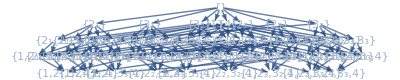

# twists | 0 | 1 | 2 | 3 | 4
# functions | 1 | 8 | 22 | 24 | 9

```mathematica
funcTree@list
```

#### Twist replacements

Replacement operations at each vertex:

```mathematica
rr[1][f_]:=replace[1,11]@f
rr[Subscript[2, 2]][f_]:=replace[{2,6,7,10},12]@f
rr[Subscript[2, 3]][f_]:=replace[{2,6},12]@f-replace[{2,6,7,10},12]@f
rr[Subscript[2, 1]][f_]:=replace[{2,7,10},12]@f-replace[{2,6,7,10},12]@f
rr[Subscript[3, 2]][f_]:=replace[{3,7,8,9},13]@f
rr[Subscript[3, 3]][f_]:=replace[{3,7,9},13]@f-replace[{3,7,8,9},13]@f
rr[Subscript[3, 1]][f_]:=replace[{3,8},13]@f-replace[{3,7,8,9},13]@f
rr[4][f_]:=replace[4,14]@f
```

Wavefunction:

```mathematica
ψ=-⟨1,2,3,4⟩+⟨1,2,3,8⟩-⟨1,2,4,7⟩-⟨1,2,4,8⟩+⟨1,2,4,10⟩-⟨1,2,7,10⟩+⟨1,3,4,6⟩+⟨1,3,4,7⟩-⟨1,3,4,9⟩-⟨1,3,5,8⟩+⟨1,3,5,9⟩+⟨1,3,6,8⟩+⟨1,3,7,10⟩-⟨1,3,8,10⟩-⟨1,4,5,6⟩+⟨1,4,5,8⟩-⟨1,4,6,8⟩-⟨1,4,6,9⟩+⟨1,4,8,10⟩+⟨1,5,6,9⟩-⟨2,3,4,6⟩-⟨2,3,6,8⟩+⟨2,4,5,6⟩-⟨2,4,5,10⟩+⟨2,4,6,8⟩+⟨2,4,6,9⟩-⟨2,4,7,9⟩-⟨2,5,6,9⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩+⟨3,4,7,9⟩-⟨3,5,7,9⟩+⟨3,5,7,10⟩-⟨3,5,8,10⟩+⟨4,5,8,10⟩;
```

Generate basis functions:

```mathematica
Subscript[f, {}]==(Subscript[F, {}]=ψ);

Table[Subscript[f, nn[[2]][[j]]]==(Subscript[F, nn[[2]][[j]]]=ψ//rr[nn[[2]][[j]][[1]]]),{j,Length@nn[[2]]}]//Column;

Table[Subscript[f, nn[[3]][[j]]]==(Subscript[F, nn[[3]][[j]]]=ψ//rr[nn[[3]][[j]][[1]]]//rr[nn[[3]][[j]][[2]]]),{j,Length@nn[[3]]}]//Column;

Table[Subscript[f, nn[[4]][[j]]]==(Subscript[F, nn[[4]][[j]]]=ψ//rr[nn[[4]][[j]][[1]]]//rr[nn[[4]][[j]][[2]]]//rr[nn[[4]][[j]][[3]]]),{j,Length@nn[[4]]}]//Column;

Table[Subscript[f, nn[[5]][[j]]]==(Subscript[F, nn[[5]][[j]]]=ψ//rr[nn[[5]][[j]][[1]]]//rr[nn[[5]][[j]][[2]]]//rr[nn[[5]][[j]][[3]]]//rr[nn[[5]][[j]][[4]]]),{j,Length@nn[[5]]}]//Column;
```

### Differential equations

```mathematica
solveCoeff;//AbsoluteTiming
```

{29.1363,Null}

#### Level 1

```mathematica
eqlvl[1]//Column
```

d[f_{}]==dL_(X1+Y12) (f_{}-f_{1})+dL_(X1-Y12) f_{1}+dL_(X4+Y34) (f_{}-f_{4})+dL_(X4-Y34) f_{4}+dL_(X2-Y12+Y23) f_{2_1}+dL_(X2-Y12-Y23) f_{2_2}+dL_(X2+Y12+Y23) (f_{}-f_{2_1}-f_{2_2}-f_{2_3})+dL_(X2+Y12-Y23) f_{2_3}+dL_(X3-Y23+Y34) f_{3_1}+dL_(X3-Y23-Y34) f_{3_2}+dL_(X3+Y23+Y34) (f_{}-f_{3_1}-f_{3_2}-f_{3_3})+dL_(X3+Y23-Y34) f_{3_3}

#### Level 2

```mathematica
eqlvl[2]//Column
```

d[f_{1}]==dL_(X1-Y12) f_{1}+dL_(X4+Y34) (f_{1}-f_{1,4})+dL_(X4-Y34) f_{1,4}+dL_(X1+X2+Y23) f_{1,2_1}+dL_(X1+X2-Y23) f_{1,2_2}+dL_(X2+Y12+Y23) (f_{1}-f_{1,2_1}-f_{1,2_2}-f_{1,2_3})+dL_(X2+Y12-Y23) f_{1,2_3}+dL_(X3-Y23+Y34) f_{1,3_1}+dL_(X3-Y23-Y34) f_{1,3_2}+dL_(X3+Y23+Y34) (f_{1}-f_{1,3_1}-f_{1,3_2}-f_{1,3_3})+dL_(X3+Y23-Y34) f_{1,3_3}
d[f_{4}]==dL_(X4-Y34) f_{4}+dL_(X1+Y12) (f_{4}-f_{1,4})+dL_(X1-Y12) f_{1,4}+dL_(X2-Y12+Y23) f_{2_1,4}+dL_(X2-Y12-Y23) f_{2_2,4}+dL_(X2+Y12+Y23) (f_{4}-f_{2_1,4}-f_{2_2,4}-f_{2_3,4})+dL_(X2+Y12-Y23) f_{2_3,4}+dL_(X3-Y23+Y34) f_{3_1,4}+dL_(X3+X4-Y23) f_{3_2,4}+dL_(X3+Y23+Y34) (f_{4}-f_{3_1,4}-f_{3_2,4}-f_{3_3,4})+dL_(X3+X4+Y23) f_{3_3,4}
d[f_{2_1}]==dL_(X2-Y12+Y23) f_{2_1}+dL_(X1+Y12) (f_{2_1}-f_{1,2_1})+dL_(X1+X2+Y23) f_{1,2_1}+dL_(X4+Y34) (f_{2_1}-f_{2_1,4})+dL_(X4-Y34) f_{2_1,4}+dL_(X3+Y23+Y34) (f_{2_1}-f_{2_1,3_1}-f_{2_1,3_2}-f_{2_1,3_3})+dL_(X3+Y23-Y34) f_{2_1,3_3}-dL_(X2+X3-Y12+Y34) f_{2_2,3_1}+dL_(X3-Y23+Y34) (f_{2_1,3_1}+f_{2_2,3_1})-dL_(X2+X3-Y12-Y34) f_{2_2,3_2}+dL_(X3-Y23-Y34) (f_{2_1,3_2}+f_{2_2,3_2})
d[f_{2_2}]==dL_(X2-Y12-Y23) f_{2_2}+dL_(X1+Y12) (f_{2_2}-f_{1,2_2})+dL_(X1+X2-Y23) f_{1,2_2}+dL_(X4+Y34) (f_{2_2}-f_{2_2,4})+dL_(X4-Y34) f_{2_2,4}+dL_(X2+X3-Y12+Y34) f_{2_2,3_1}+dL_(X2+X3-Y12-Y34) f_{2_2,3_2}+dL_(X3+Y23+Y34) (f_{2_2}-f_{2_2,3_1}-f_{2_2,3_2}-f_{2_2,3_3})+dL_(X3+Y23-Y34) f_{2_2,3_3}
d[f_{2_3}]==dL_(X2+Y12-Y23) f_{2_3}-dL_(X1+X2-Y23) f_{1,2_2}+dL_(X1+Y12) (f_{2_3}-f_{1,2_3})+dL_(X1-Y12) (f_{1,2_2}+f_{1,2_3})+dL_(X4+Y34) (f_{2_3}-f_{2_3,4})+dL_(X4-Y34) f_{2_3,4}+dL_(X2+X3+Y12+Y34) f_{2_3,3_1}+dL_(X2+X3+Y12-Y34) f_{2_3,3_2}+dL_(X3+Y23+Y34) (f_{2_3}-f_{2_3,3_1}-f_{2_3,3_2}-f_{2_3,3_3})+dL_(X3+Y23-Y34) f_{2_3,3_3}
d[f_{3_1}]==dL_(X3-Y23+Y34) f_{3_1}+dL_(X1+Y12) (f_{3_1}-f_{1,3_1})+dL_(X1-Y12) f_{1,3_1}+dL_(X2-Y12+Y23) f_{2_1,3_1}+dL_(X2+X3-Y12+Y34) f_{2_2,3_1}+dL_(X2+Y12+Y23) (f_{3_1}-f_{2_1,3_1}-f_{2_2,3_1}-f_{2_3,3_1})+dL_(X2+X3+Y12+Y34) f_{2_3,3_1}+dL_(X4+Y34) (f_{3_1}-f_{3_1,4})-dL_(X3+X4-Y23) f_{3_2,4}+dL_(X4-Y34) (f_{3_1,4}+f_{3_2,4})
d[f_{3_2}]==dL_(X3-Y23-Y34) f_{3_2}+dL_(X1+Y12) (f_{3_2}-f_{1,3_2})+dL_(X1-Y12) f_{1,3_2}+dL_(X2-Y12+Y23) f_{2_1,3_2}+dL_(X2+X3-Y12-Y34) f_{2_2,3_2}+dL_(X2+Y12+Y23) (f_{3_2}-f_{2_1,3_2}-f_{2_2,3_2}-f_{2_3,3_2})+dL_(X2+X3+Y12-Y34) f_{2_3,3_2}+dL_(X4+Y34) (f_{3_2}-f_{3_2,4})+dL_(X3+X4-Y23) f_{3_2,4}
d[f_{3_3}]==dL_(X3+Y23-Y34) f_{3_3}+dL_(X1+Y12) (f_{3_3}-f_{1,3_3})+dL_(X1-Y12) f_{1,3_3}+dL_(X2-Y12+Y23) f_{2_1,3_3}-dL_(X2+X3-Y12-Y34) f_{2_2,3_2}+dL_(X2-Y12-Y23) (f_{2_2,3_2}+f_{2_2,3_3})-dL_(X2+X3+Y12-Y34) f_{2_3,3_2}+dL_(X2+Y12+Y23) (f_{3_3}-f_{2_1,3_3}-f_{2_2,3_3}-f_{2_3,3_3})+dL_(X2+Y12-Y23) (f_{2_3,3_2}+f_{2_3,3_3})+dL_(X4+Y34) (f_{3_3}-f_{3_3,4})+dL_(X3+X4+Y23) f_{3_3,4}

#### Level 3

```mathematica
eqlvl[3]//Column
```

d[f_{1,4}]==dL_(X1-Y12) f_{1,4}+dL_(X4-Y34) f_{1,4}+dL_(X1+X2+Y23) f_{1,2_1,4}+dL_(X1+X2-Y23) f_{1,2_2,4}+dL_(X2+Y12+Y23) (f_{1,4}-f_{1,2_1,4}-f_{1,2_2,4}-f_{1,2_3,4})+dL_(X2+Y12-Y23) f_{1,2_3,4}+dL_(X3-Y23+Y34) f_{1,3_1,4}+dL_(X3+X4-Y23) f_{1,3_2,4}+dL_(X3+Y23+Y34) (f_{1,4}-f_{1,3_1,4}-f_{1,3_2,4}-f_{1,3_3,4})+dL_(X3+X4+Y23) f_{1,3_3,4}
d[f_{1,2_1}]==2 dL_(X1+X2+Y23) f_{1,2_1}+dL_(X4+Y34) (f_{1,2_1}-f_{1,2_1,4})+dL_(X4-Y34) f_{1,2_1,4}+dL_(X3+Y23+Y34) (f_{1,2_1}-f_{1,2_1,3_1}-f_{1,2_1,3_2}-f_{1,2_1,3_3})+dL_(X3+Y23-Y34) f_{1,2_1,3_3}-dL_(X1+X2+X3+Y34) f_{1,2_2,3_1}+dL_(X3-Y23+Y34) (f_{1,2_1,3_1}+f_{1,2_2,3_1})-dL_(X1+X2+X3-Y34) f_{1,2_2,3_2}+dL_(X3-Y23-Y34) (f_{1,2_1,3_2}+f_{1,2_2,3_2})
d[f_{1,2_2}]==2 dL_(X1+X2-Y23) f_{1,2_2}+dL_(X4+Y34) (f_{1,2_2}-f_{1,2_2,4})+dL_(X4-Y34) f_{1,2_2,4}+dL_(X1+X2+X3+Y34) f_{1,2_2,3_1}+dL_(X1+X2+X3-Y34) f_{1,2_2,3_2}+dL_(X3+Y23+Y34) (f_{1,2_2}-f_{1,2_2,3_1}-f_{1,2_2,3_2}-f_{1,2_2,3_3})+dL_(X3+Y23-Y34) f_{1,2_2,3_3}
d[f_{1,2_3}]==-dL_(X1+X2-Y23) f_{1,2_2}+dL_(X2+Y12-Y23) f_{1,2_3}+dL_(X1-Y12) (f_{1,2_2}+f_{1,2_3})+dL_(X4+Y34) (f_{1,2_3}-f_{1,2_3,4})+dL_(X4-Y34) f_{1,2_3,4}+dL_(X2+X3+Y12+Y34) f_{1,2_3,3_1}+dL_(X2+X3+Y12-Y34) f_{1,2_3,3_2}+dL_(X3+Y23+Y34) (f_{1,2_3}-f_{1,2_3,3_1}-f_{1,2_3,3_2}-f_{1,2_3,3_3})+dL_(X3+Y23-Y34) f_{1,2_3,3_3}
d[f_{1,3_1}]==dL_(X1-Y12) f_{1,3_1}+dL_(X3-Y23+Y34) f_{1,3_1}+dL_(X1+X2+Y23) f_{1,2_1,3_1}+dL_(X1+X2+X3+Y34) f_{1,2_2,3_1}+dL_(X2+Y12+Y23) (f_{1,3_1}-f_{1,2_1,3_1}-f_{1,2_2,3_1}-f_{1,2_3,3_1})+dL_(X2+X3+Y12+Y34) f_{1,2_3,3_1}+dL_(X4+Y34) (f_{1,3_1}-f_{1,3_1,4})-dL_(X3+X4-Y23) f_{1,3_2,4}+dL_(X4-Y34) (f_{1,3_1,4}+f_{1,3_2,4})
d[f_{1,3_2}]==dL_(X1-Y12) f_{1,3_2}+dL_(X3-Y23-Y34) f_{1,3_2}+dL_(X1+X2+Y23) f_{1,2_1,3_2}+dL_(X1+X2+X3-Y34) f_{1,2_2,3_2}+dL_(X2+Y12+Y23) (f_{1,3_2}-f_{1,2_1,3_2}-f_{1,2_2,3_2}-f_{1,2_3,3_2})+dL_(X2+X3+Y12-Y34) f_{1,2_3,3_2}+dL_(X4+Y34) (f_{1,3_2}-f_{1,3_2,4})+dL_(X3+X4-Y23) f_{1,3_2,4}
d[f_{1,3_3}]==dL_(X1-Y12) f_{1,3_3}+dL_(X3+Y23-Y34) f_{1,3_3}+dL_(X1+X2+Y23) f_{1,2_1,3_3}-dL_(X1+X2+X3-Y34) f_{1,2_2,3_2}+dL_(X1+X2-Y23) (f_{1,2_2,3_2}+f_{1,2_2,3_3})-dL_(X2+X3+Y12-Y34) f_{1,2_3,3_2}+dL_(X2+Y12+Y23) (f_{1,3_3}-f_{1,2_1,3_3}-f_{1,2_2,3_3}-f_{1,2_3,3_3})+dL_(X2+Y12-Y23) (f_{1,2_3,3_2}+f_{1,2_3,3_3})+dL_(X4+Y34) (f_{1,3_3}-f_{1,3_3,4})+dL_(X3+X4+Y23) f_{1,3_3,4}
d[f_{2_1,4}]==dL_(X2-Y12+Y23) f_{2_1,4}+dL_(X4-Y34) f_{2_1,4}+dL_(X1+Y12) (f_{2_1,4}-f_{1,2_1,4})+dL_(X1+X2+Y23) f_{1,2_1,4}+dL_(X3+Y23+Y34) (f_{2_1,4}-f_{2_1,3_1,4}-f_{2_1,3_2,4}-f_{2_1,3_3,4})+dL_(X3+X4+Y23) f_{2_1,3_3,4}-dL_(X2+X3-Y12+Y34) f_{2_2,3_1,4}+dL_(X3-Y23+Y34) (f_{2_1,3_1,4}+f_{2_2,3_1,4})-dL_(X2+X3+X4-Y12) f_{2_2,3_2,4}+dL_(X3+X4-Y23) (f_{2_1,3_2,4}+f_{2_2,3_2,4})
d[f_{2_1,3_1}]==dL_(X2-Y12+Y23) f_{2_1,3_1}-dL_(X2+X3-Y12+Y34) f_{2_2,3_1}+dL_(X3-Y23+Y34) (f_{2_1,3_1}+f_{2_2,3_1})+dL_(X1+Y12) (f_{2_1,3_1}-f_{1,2_1,3_1})+dL_(X1+X2+Y23) f_{1,2_1,3_1}+dL_(X4+Y34) (f_{2_1,3_1}-f_{2_1,3_1,4})+dL_(X4-Y34) (f_{2_1,3_1,4}+f_{2_1,3_2,4})+dL_(X3+X4-Y23) (-f_{2_1,3_2,4}-f_{2_2,3_2,4})+dL_(X2+X3+X4-Y12) f_{2_2,3_2,4}
d[f_{2_1,3_2}]==dL_(X2-Y12+Y23) f_{2_1,3_2}-dL_(X2+X3-Y12-Y34) f_{2_2,3_2}+dL_(X3-Y23-Y34) (f_{2_1,3_2}+f_{2_2,3_2})+dL_(X1+Y12) (f_{2_1,3_2}-f_{1,2_1,3_2})+dL_(X1+X2+Y23) f_{1,2_1,3_2}+dL_(X4+Y34) (f_{2_1,3_2}-f_{2_1,3_2,4})-dL_(X2+X3+X4-Y12) f_{2_2,3_2,4}+dL_(X3+X4-Y23) (f_{2_1,3_2,4}+f_{2_2,3_2,4})
d[f_{2_1,3_3}]==dL_(X2-Y12+Y23) f_{2_1,3_3}+dL_(X3+Y23-Y34) f_{2_1,3_3}+dL_(X1+Y12) (f_{2_1,3_3}-f_{1,2_1,3_3})+dL_(X1+X2+Y23) f_{1,2_1,3_3}+dL_(X4+Y34) (f_{2_1,3_3}-f_{2_1,3_3,4})+dL_(X3+X4+Y23) f_{2_1,3_3,4}
d[f_{2_2,4}]==dL_(X2-Y12-Y23) f_{2_2,4}+dL_(X4-Y34) f_{2_2,4}+dL_(X1+Y12) (f_{2_2,4}-f_{1,2_2,4})+dL_(X1+X2-Y23) f_{1,2_2,4}+dL_(X2+X3-Y12+Y34) f_{2_2,3_1,4}+dL_(X2+X3+X4-Y12) f_{2_2,3_2,4}+dL_(X3+Y23+Y34) (f_{2_2,4}-f_{2_2,3_1,4}-f_{2_2,3_2,4}-f_{2_2,3_3,4})+dL_(X3+X4+Y23) f_{2_2,3_3,4}
d[f_{2_2,3_1}]==2 dL_(X2+X3-Y12+Y34) f_{2_2,3_1}+dL_(X1+Y12) (f_{2_2,3_1}-f_{1,2_2,3_1})+dL_(X1+X2+X3+Y34) f_{1,2_2,3_1}+dL_(X4+Y34) (f_{2_2,3_1}-f_{2_2,3_1,4})-dL_(X2+X3+X4-Y12) f_{2_2,3_2,4}+dL_(X4-Y34) (f_{2_2,3_1,4}+f_{2_2,3_2,4})
d[f_{2_2,3_2}]==2 dL_(X2+X3-Y12-Y34) f_{2_2,3_2}+dL_(X1+Y12) (f_{2_2,3_2}-f_{1,2_2,3_2})+dL_(X1+X2+X3-Y34) f_{1,2_2,3_2}+dL_(X4+Y34) (f_{2_2,3_2}-f_{2_2,3_2,4})+dL_(X2+X3+X4-Y12) f_{2_2,3_2,4}
d[f_{2_2,3_3}]==-dL_(X2+X3-Y12-Y34) f_{2_2,3_2}+dL_(X3+Y23-Y34) f_{2_2,3_3}+dL_(X2-Y12-Y23) (f_{2_2,3_2}+f_{2_2,3_3})-dL_(X1+X2+X3-Y34) f_{1,2_2,3_2}+dL_(X1+Y12) (f_{2_2,3_3}-f_{1,2_2,3_3})+dL_(X1+X2-Y23) (f_{1,2_2,3_2}+f_{1,2_2,3_3})+dL_(X4+Y34) (f_{2_2,3_3}-f_{2_2,3_3,4})+dL_(X3+X4+Y23) f_{2_2,3_3,4}
d[f_{2_3,4}]==dL_(X2+Y12-Y23) f_{2_3,4}+dL_(X4-Y34) f_{2_3,4}-dL_(X1+X2-Y23) f_{1,2_2,4}+dL_(X1+Y12) (f_{2_3,4}-f_{1,2_3,4})+dL_(X1-Y12) (f_{1,2_2,4}+f_{1,2_3,4})+dL_(X2+X3+Y12+Y34) f_{2_3,3_1,4}+dL_(X2+X3+X4+Y12) f_{2_3,3_2,4}+dL_(X3+Y23+Y34) (f_{2_3,4}-f_{2_3,3_1,4}-f_{2_3,3_2,4}-f_{2_3,3_3,4})+dL_(X3+X4+Y23) f_{2_3,3_3,4}
d[f_{2_3,3_1}]==2 dL_(X2+X3+Y12+Y34) f_{2_3,3_1}-dL_(X1+X2+X3+Y34) f_{1,2_2,3_1}+dL_(X1+Y12) (f_{2_3,3_1}-f_{1,2_3,3_1})+dL_(X1-Y12) (f_{1,2_2,3_1}+f_{1,2_3,3_1})+dL_(X4+Y34) (f_{2_3,3_1}-f_{2_3,3_1,4})-dL_(X2+X3+X4+Y12) f_{2_3,3_2,4}+dL_(X4-Y34) (f_{2_3,3_1,4}+f_{2_3,3_2,4})
d[f_{2_3,3_2}]==2 dL_(X2+X3+Y12-Y34) f_{2_3,3_2}-dL_(X1+X2+X3-Y34) f_{1,2_2,3_2}+dL_(X1+Y12) (f_{2_3,3_2}-f_{1,2_3,3_2})+dL_(X1-Y12) (f_{1,2_2,3_2}+f_{1,2_3,3_2})+dL_(X4+Y34) (f_{2_3,3_2}-f_{2_3,3_2,4})+dL_(X2+X3+X4+Y12) f_{2_3,3_2,4}
d[f_{2_3,3_3}]==-dL_(X2+X3+Y12-Y34) f_{2_3,3_2}+dL_(X3+Y23-Y34) f_{2_3,3_3}+dL_(X2+Y12-Y23) (f_{2_3,3_2}+f_{2_3,3_3})+dL_(X1+X2+X3-Y34) f_{1,2_2,3_2}+dL_(X1+X2-Y23) (-f_{1,2_2,3_2}-f_{1,2_2,3_3})+dL_(X1+Y12) (f_{2_3,3_3}-f_{1,2_3,3_3})+dL_(X1-Y12) (f_{1,2_2,3_3}+f_{1,2_3,3_3})+dL_(X4+Y34) (f_{2_3,3_3}-f_{2_3,3_3,4})+dL_(X3+X4+Y23) f_{2_3,3_3,4}
d[f_{3_1,4}]==dL_(X3-Y23+Y34) f_{3_1,4}-dL_(X3+X4-Y23) f_{3_2,4}+dL_(X4-Y34) (f_{3_1,4}+f_{3_2,4})+dL_(X1+Y12) (f_{3_1,4}-f_{1,3_1,4})+dL_(X1-Y12) f_{1,3_1,4}+dL_(X2-Y12+Y23) f_{2_1,3_1,4}+dL_(X2+X3-Y12+Y34) f_{2_2,3_1,4}+dL_(X2+Y12+Y23) (f_{3_1,4}-f_{2_1,3_1,4}-f_{2_2,3_1,4}-f_{2_3,3_1,4})+dL_(X2+X3+Y12+Y34) f_{2_3,3_1,4}
d[f_{3_2,4}]==2 dL_(X3+X4-Y23) f_{3_2,4}+dL_(X1+Y12) (f_{3_2,4}-f_{1,3_2,4})+dL_(X1-Y12) f_{1,3_2,4}+dL_(X2-Y12+Y23) f_{2_1,3_2,4}+dL_(X2+X3+X4-Y12) f_{2_2,3_2,4}+dL_(X2+Y12+Y23) (f_{3_2,4}-f_{2_1,3_2,4}-f_{2_2,3_2,4}-f_{2_3,3_2,4})+dL_(X2+X3+X4+Y12) f_{2_3,3_2,4}
d[f_{3_3,4}]==2 dL_(X3+X4+Y23) f_{3_3,4}+dL_(X1+Y12) (f_{3_3,4}-f_{1,3_3,4})+dL_(X1-Y12) f_{1,3_3,4}+dL_(X2-Y12+Y23) f_{2_1,3_3,4}-dL_(X2+X3+X4-Y12) f_{2_2,3_2,4}+dL_(X2-Y12-Y23) (f_{2_2,3_2,4}+f_{2_2,3_3,4})-dL_(X2+X3+X4+Y12) f_{2_3,3_2,4}+dL_(X2+Y12+Y23) (f_{3_3,4}-f_{2_1,3_3,4}-f_{2_2,3_3,4}-f_{2_3,3_3,4})+dL_(X2+Y12-Y23) (f_{2_3,3_2,4}+f_{2_3,3_3,4})

#### Level 4

```mathematica
eqlvl[4]//Column
```

d[f_{1,2_1,4}]==2 dL_(X1+X2+Y23) f_{1,2_1,4}+dL_(X4-Y34) f_{1,2_1,4}+dL_(X3+Y23+Y34) (f_{1,2_1,4}-f_{1,2_1,3_1,4}-f_{1,2_1,3_2,4}-f_{1,2_1,3_3,4})+dL_(X3+X4+Y23) f_{1,2_1,3_3,4}-dL_(X1+X2+X3+Y34) f_{1,2_2,3_1,4}+dL_(X3-Y23+Y34) (f_{1,2_1,3_1,4}+f_{1,2_2,3_1,4})-dL_(X1+X2+X3+X4) f_{1,2_2,3_2,4}+dL_(X3+X4-Y23) (f_{1,2_1,3_2,4}+f_{1,2_2,3_2,4})
d[f_{1,2_1,3_1}]==2 dL_(X1+X2+Y23) f_{1,2_1,3_1}-dL_(X1+X2+X3+Y34) f_{1,2_2,3_1}+dL_(X3-Y23+Y34) (f_{1,2_1,3_1}+f_{1,2_2,3_1})+dL_(X4+Y34) (f_{1,2_1,3_1}-f_{1,2_1,3_1,4})+dL_(X4-Y34) (f_{1,2_1,3_1,4}+f_{1,2_1,3_2,4})+dL_(X3+X4-Y23) (-f_{1,2_1,3_2,4}-f_{1,2_2,3_2,4})+dL_(X1+X2+X3+X4) f_{1,2_2,3_2,4}
d[f_{1,2_1,3_2}]==2 dL_(X1+X2+Y23) f_{1,2_1,3_2}-dL_(X1+X2+X3-Y34) f_{1,2_2,3_2}+dL_(X3-Y23-Y34) (f_{1,2_1,3_2}+f_{1,2_2,3_2})+dL_(X4+Y34) (f_{1,2_1,3_2}-f_{1,2_1,3_2,4})-dL_(X1+X2+X3+X4) f_{1,2_2,3_2,4}+dL_(X3+X4-Y23) (f_{1,2_1,3_2,4}+f_{1,2_2,3_2,4})
d[f_{1,2_1,3_3}]==2 dL_(X1+X2+Y23) f_{1,2_1,3_3}+dL_(X3+Y23-Y34) f_{1,2_1,3_3}+dL_(X4+Y34) (f_{1,2_1,3_3}-f_{1,2_1,3_3,4})+dL_(X3+X4+Y23) f_{1,2_1,3_3,4}
d[f_{1,2_2,4}]==2 dL_(X1+X2-Y23) f_{1,2_2,4}+dL_(X4-Y34) f_{1,2_2,4}+dL_(X1+X2+X3+Y34) f_{1,2_2,3_1,4}+dL_(X1+X2+X3+X4) f_{1,2_2,3_2,4}+dL_(X3+Y23+Y34) (f_{1,2_2,4}-f_{1,2_2,3_1,4}-f_{1,2_2,3_2,4}-f_{1,2_2,3_3,4})+dL_(X3+X4+Y23) f_{1,2_2,3_3,4}
d[f_{1,2_2,3_1}]==3 dL_(X1+X2+X3+Y34) f_{1,2_2,3_1}+dL_(X4+Y34) (f_{1,2_2,3_1}-f_{1,2_2,3_1,4})-dL_(X1+X2+X3+X4) f_{1,2_2,3_2,4}+dL_(X4-Y34) (f_{1,2_2,3_1,4}+f_{1,2_2,3_2,4})
d[f_{1,2_2,3_2}]==3 dL_(X1+X2+X3-Y34) f_{1,2_2,3_2}+dL_(X4+Y34) (f_{1,2_2,3_2}-f_{1,2_2,3_2,4})+dL_(X1+X2+X3+X4) f_{1,2_2,3_2,4}
d[f_{1,2_2,3_3}]==-2 dL_(X1+X2+X3-Y34) f_{1,2_2,3_2}+dL_(X3+Y23-Y34) f_{1,2_2,3_3}+dL_(X1+X2-Y23) (2 f_{1,2_2,3_2}+2 f_{1,2_2,3_3})+dL_(X4+Y34) (f_{1,2_2,3_3}-f_{1,2_2,3_3,4})+dL_(X3+X4+Y23) f_{1,2_2,3_3,4}
d[f_{1,2_3,4}]==-dL_(X1+X2-Y23) f_{1,2_2,4}+dL_(X2+Y12-Y23) f_{1,2_3,4}+dL_(X4-Y34) f_{1,2_3,4}+dL_(X1-Y12) (f_{1,2_2,4}+f_{1,2_3,4})+dL_(X2+X3+Y12+Y34) f_{1,2_3,3_1,4}+dL_(X2+X3+X4+Y12) f_{1,2_3,3_2,4}+dL_(X3+Y23+Y34) (f_{1,2_3,4}-f_{1,2_3,3_1,4}-f_{1,2_3,3_2,4}-f_{1,2_3,3_3,4})+dL_(X3+X4+Y23) f_{1,2_3,3_3,4}
d[f_{1,2_3,3_1}]==-dL_(X1+X2+X3+Y34) f_{1,2_2,3_1}+2 dL_(X2+X3+Y12+Y34) f_{1,2_3,3_1}+dL_(X1-Y12) (f_{1,2_2,3_1}+f_{1,2_3,3_1})+dL_(X4+Y34) (f_{1,2_3,3_1}-f_{1,2_3,3_1,4})-dL_(X2+X3+X4+Y12) f_{1,2_3,3_2,4}+dL_(X4-Y34) (f_{1,2_3,3_1,4}+f_{1,2_3,3_2,4})
d[f_{1,2_3,3_2}]==-dL_(X1+X2+X3-Y34) f_{1,2_2,3_2}+2 dL_(X2+X3+Y12-Y34) f_{1,2_3,3_2}+dL_(X1-Y12) (f_{1,2_2,3_2}+f_{1,2_3,3_2})+dL_(X4+Y34) (f_{1,2_3,3_2}-f_{1,2_3,3_2,4})+dL_(X2+X3+X4+Y12) f_{1,2_3,3_2,4}
d[f_{1,2_3,3_3}]==dL_(X1+X2+X3-Y34) f_{1,2_2,3_2}+dL_(X1+X2-Y23) (-f_{1,2_2,3_2}-f_{1,2_2,3_3})-dL_(X2+X3+Y12-Y34) f_{1,2_3,3_2}+dL_(X3+Y23-Y34) f_{1,2_3,3_3}+dL_(X1-Y12) (f_{1,2_2,3_3}+f_{1,2_3,3_3})+dL_(X2+Y12-Y23) (f_{1,2_3,3_2}+f_{1,2_3,3_3})+dL_(X4+Y34) (f_{1,2_3,3_3}-f_{1,2_3,3_3,4})+dL_(X3+X4+Y23) f_{1,2_3,3_3,4}
d[f_{1,3_1,4}]==dL_(X1-Y12) f_{1,3_1,4}+dL_(X3-Y23+Y34) f_{1,3_1,4}-dL_(X3+X4-Y23) f_{1,3_2,4}+dL_(X4-Y34) (f_{1,3_1,4}+f_{1,3_2,4})+dL_(X1+X2+Y23) f_{1,2_1,3_1,4}+dL_(X1+X2+X3+Y34) f_{1,2_2,3_1,4}+dL_(X2+Y12+Y23) (f_{1,3_1,4}-f_{1,2_1,3_1,4}-f_{1,2_2,3_1,4}-f_{1,2_3,3_1,4})+dL_(X2+X3+Y12+Y34) f_{1,2_3,3_1,4}
d[f_{1,3_2,4}]==dL_(X1-Y12) f_{1,3_2,4}+2 dL_(X3+X4-Y23) f_{1,3_2,4}+dL_(X1+X2+Y23) f_{1,2_1,3_2,4}+dL_(X1+X2+X3+X4) f_{1,2_2,3_2,4}+dL_(X2+Y12+Y23) (f_{1,3_2,4}-f_{1,2_1,3_2,4}-f_{1,2_2,3_2,4}-f_{1,2_3,3_2,4})+dL_(X2+X3+X4+Y12) f_{1,2_3,3_2,4}
d[f_{1,3_3,4}]==dL_(X1-Y12) f_{1,3_3,4}+2 dL_(X3+X4+Y23) f_{1,3_3,4}+dL_(X1+X2+Y23) f_{1,2_1,3_3,4}-dL_(X1+X2+X3+X4) f_{1,2_2,3_2,4}+dL_(X1+X2-Y23) (f_{1,2_2,3_2,4}+f_{1,2_2,3_3,4})-dL_(X2+X3+X4+Y12) f_{1,2_3,3_2,4}+dL_(X2+Y12+Y23) (f_{1,3_3,4}-f_{1,2_1,3_3,4}-f_{1,2_2,3_3,4}-f_{1,2_3,3_3,4})+dL_(X2+Y12-Y23) (f_{1,2_3,3_2,4}+f_{1,2_3,3_3,4})
d[f_{2_1,3_1,4}]==dL_(X2-Y12+Y23) f_{2_1,3_1,4}+dL_(X4-Y34) (f_{2_1,3_1,4}+f_{2_1,3_2,4})-dL_(X2+X3-Y12+Y34) f_{2_2,3_1,4}+dL_(X3-Y23+Y34) (f_{2_1,3_1,4}+f_{2_2,3_1,4})+dL_(X3+X4-Y23) (-f_{2_1,3_2,4}-f_{2_2,3_2,4})+dL_(X2+X3+X4-Y12) f_{2_2,3_2,4}+dL_(X1+Y12) (f_{2_1,3_1,4}-f_{1,2_1,3_1,4})+dL_(X1+X2+Y23) f_{1,2_1,3_1,4}
d[f_{2_1,3_2,4}]==dL_(X2-Y12+Y23) f_{2_1,3_2,4}-2 dL_(X2+X3+X4-Y12) f_{2_2,3_2,4}+dL_(X3+X4-Y23) (2 f_{2_1,3_2,4}+2 f_{2_2,3_2,4})+dL_(X1+Y12) (f_{2_1,3_2,4}-f_{1,2_1,3_2,4})+dL_(X1+X2+Y23) f_{1,2_1,3_2,4}
d[f_{2_1,3_3,4}]==2 dL_(X3+X4+Y23) f_{2_1,3_3,4}+dL_(X2-Y12+Y23) f_{2_1,3_3,4}+dL_(X1+Y12) (f_{2_1,3_3,4}-f_{1,2_1,3_3,4})+dL_(X1+X2+Y23) f_{1,2_1,3_3,4}
d[f_{2_2,3_1,4}]==2 dL_(X2+X3-Y12+Y34) f_{2_2,3_1,4}-dL_(X2+X3+X4-Y12) f_{2_2,3_2,4}+dL_(X4-Y34) (f_{2_2,3_1,4}+f_{2_2,3_2,4})+dL_(X1+Y12) (f_{2_2,3_1,4}-f_{1,2_2,3_1,4})+dL_(X1+X2+X3+Y34) f_{1,2_2,3_1,4}
d[f_{2_2,3_2,4}]==3 dL_(X2+X3+X4-Y12) f_{2_2,3_2,4}+dL_(X1+Y12) (f_{2_2,3_2,4}-f_{1,2_2,3_2,4})+dL_(X1+X2+X3+X4) f_{1,2_2,3_2,4}
d[f_{2_2,3_3,4}]==-dL_(X2+X3+X4-Y12) f_{2_2,3_2,4}+2 dL_(X3+X4+Y23) f_{2_2,3_3,4}+dL_(X2-Y12-Y23) (f_{2_2,3_2,4}+f_{2_2,3_3,4})-dL_(X1+X2+X3+X4) f_{1,2_2,3_2,4}+dL_(X1+Y12) (f_{2_2,3_3,4}-f_{1,2_2,3_3,4})+dL_(X1+X2-Y23) (f_{1,2_2,3_2,4}+f_{1,2_2,3_3,4})
d[f_{2_3,3_1,4}]==2 dL_(X2+X3+Y12+Y34) f_{2_3,3_1,4}-dL_(X2+X3+X4+Y12) f_{2_3,3_2,4}+dL_(X4-Y34) (f_{2_3,3_1,4}+f_{2_3,3_2,4})-dL_(X1+X2+X3+Y34) f_{1,2_2,3_1,4}+dL_(X1+Y12) (f_{2_3,3_1,4}-f_{1,2_3,3_1,4})+dL_(X1-Y12) (f_{1,2_2,3_1,4}+f_{1,2_3,3_1,4})
d[f_{2_3,3_2,4}]==3 dL_(X2+X3+X4+Y12) f_{2_3,3_2,4}-dL_(X1+X2+X3+X4) f_{1,2_2,3_2,4}+dL_(X1+Y12) (f_{2_3,3_2,4}-f_{1,2_3,3_2,4})+dL_(X1-Y12) (f_{1,2_2,3_2,4}+f_{1,2_3,3_2,4})
d[f_{2_3,3_3,4}]==-dL_(X2+X3+X4+Y12) f_{2_3,3_2,4}+2 dL_(X3+X4+Y23) f_{2_3,3_3,4}+dL_(X2+Y12-Y23) (f_{2_3,3_2,4}+f_{2_3,3_3,4})+dL_(X1+X2+X3+X4) f_{1,2_2,3_2,4}+dL_(X1+X2-Y23) (-f_{1,2_2,3_2,4}-f_{1,2_2,3_3,4})+dL_(X1+Y12) (f_{2_3,3_3,4}-f_{1,2_3,3_3,4})+dL_(X1-Y12) (f_{1,2_2,3_3,4}+f_{1,2_3,3_3,4})

#### Level 5

```mathematica
eqlvl[5]//Column
```

d[f_{1,2_1,3_1,4}]==2 dL_(X1+X2+Y23) f_{1,2_1,3_1,4}+dL_(X4-Y34) (f_{1,2_1,3_1,4}+f_{1,2_1,3_2,4})-dL_(X1+X2+X3+Y34) f_{1,2_2,3_1,4}+dL_(X3-Y23+Y34) (f_{1,2_1,3_1,4}+f_{1,2_2,3_1,4})+dL_(X3+X4-Y23) (-f_{1,2_1,3_2,4}-f_{1,2_2,3_2,4})+dL_(X1+X2+X3+X4) f_{1,2_2,3_2,4}
d[f_{1,2_1,3_2,4}]==2 dL_(X1+X2+Y23) f_{1,2_1,3_2,4}-2 dL_(X1+X2+X3+X4) f_{1,2_2,3_2,4}+dL_(X3+X4-Y23) (2 f_{1,2_1,3_2,4}+2 f_{1,2_2,3_2,4})
d[f_{1,2_1,3_3,4}]==2 dL_(X1+X2+Y23) f_{1,2_1,3_3,4}+2 dL_(X3+X4+Y23) f_{1,2_1,3_3,4}
d[f_{1,2_2,3_1,4}]==3 dL_(X1+X2+X3+Y34) f_{1,2_2,3_1,4}-dL_(X1+X2+X3+X4) f_{1,2_2,3_2,4}+dL_(X4-Y34) (f_{1,2_2,3_1,4}+f_{1,2_2,3_2,4})
d[f_{1,2_2,3_2,4}]==4 dL_(X1+X2+X3+X4) f_{1,2_2,3_2,4}
d[f_{1,2_2,3_3,4}]==-2 dL_(X1+X2+X3+X4) f_{1,2_2,3_2,4}+2 dL_(X3+X4+Y23) f_{1,2_2,3_3,4}+dL_(X1+X2-Y23) (2 f_{1,2_2,3_2,4}+2 f_{1,2_2,3_3,4})
d[f_{1,2_3,3_1,4}]==-dL_(X1+X2+X3+Y34) f_{1,2_2,3_1,4}+2 dL_(X2+X3+Y12+Y34) f_{1,2_3,3_1,4}+dL_(X1-Y12) (f_{1,2_2,3_1,4}+f_{1,2_3,3_1,4})-dL_(X2+X3+X4+Y12) f_{1,2_3,3_2,4}+dL_(X4-Y34) (f_{1,2_3,3_1,4}+f_{1,2_3,3_2,4})
d[f_{1,2_3,3_2,4}]==-dL_(X1+X2+X3+X4) f_{1,2_2,3_2,4}+3 dL_(X2+X3+X4+Y12) f_{1,2_3,3_2,4}+dL_(X1-Y12) (f_{1,2_2,3_2,4}+f_{1,2_3,3_2,4})
d[f_{1,2_3,3_3,4}]==dL_(X1+X2+X3+X4) f_{1,2_2,3_2,4}+dL_(X1+X2-Y23) (-f_{1,2_2,3_2,4}-f_{1,2_2,3_3,4})-dL_(X2+X3+X4+Y12) f_{1,2_3,3_2,4}+2 dL_(X3+X4+Y23) f_{1,2_3,3_3,4}+dL_(X1-Y12) (f_{1,2_2,3_3,4}+f_{1,2_3,3_3,4})+dL_(X2+Y12-Y23) (f_{1,2_3,3_2,4}+f_{1,2_3,3_3,4})

### A matrix

```mathematica
flist=Flatten[Table[Subscript[f, nn[[l]][[m]]],{l,nsite+1},{m,Length@nn[[l]]}],1];
```

```mathematica
Flatten[Table[eqlvl[i][[m]][[2]],{i,0,nsite+1},{m,Length@eqlvl[i]}],1];
Amtx=Table[Coefficient[%[[i]],flist],{i,4^(nsite-1)}];
```

Check flatness:

```mathematica
A=Amtx/.Subscript[dL, a_]:>Dt@Log[a];
vars={X1,X2,X3,X4,Y12,Y23,Y34};
DeleteDuplicates@Flatten@Table[Coefficient[A,Dt[vars[[i]]]].Coefficient[A,Dt[vars[[j]]]]-Coefficient[A,Dt[vars[[j]]]].Coefficient[A,Dt[vars[[i]]]]//Simplify,{i,Length@vars},{j,Length@vars}]
```

{0}

### d^2=0

Three-letter relations:

```mathematica
DeleteDuplicates@DeleteCases[Flatten[Table[If[(-letters[[i]]+letters[[j]]+letters[[k]]//Simplify)===0∧i=!=j∧i=!=k∧j=!=k,{i,j,k},0],{i,Length@letters},{j,Length@letters},{k,Length@letters}],2],0];
reltab=Subscript[dL, letters[[#1]]]⋀Subscript[dL, letters[[#3]]]+Subscript[dL, letters[[#2]]]⋀Subscript[dL, letters[[#1]]]-Subscript[dL, letters[[#2]]]⋀Subscript[dL, letters[[#3]]]&@@@%//dLsimp;
```

Independent relations:

```mathematica
dLrel=Table[If[reltab[[i,1]][[1]]===-1,-reltab[[i]],reltab[[i]]],{i,Length@reltab}]//DeleteDuplicates;
dLsub=Table[%[[i]][[1]]->Subscript[R, i]-%[[i]][[2]]-%[[i]][[3]],{i,Length@%}];
%//Length
```

38

Taking d^2:

```mathematica
dfeq=Flatten@Table[eqlvl[l][[m]],{l,5},{m,Length@nn[[l]]}];
dfsub=dfeq/.a_==b_:>a->b;
ddeq=Flatten@Table[d[Subscript[f, nn[[l]][[m]]]],{l,5},{m,Length@nn[[l]]}]/.d[f_]:>(d^2)[f]==dd[f];
```

```mathematica
ddeq/.dLsub/.Subscript[R, _]->0//Simplify
```

{d^2[f_{}]==0,d^2[f_{1}]==0,d^2[f_{4}]==0,d^2[f_{2_1}]==0,d^2[f_{2_2}]==0,d^2[f_{2_3}]==0,d^2[f_{3_1}]==0,d^2[f_{3_2}]==0,d^2[f_{3_3}]==0,d^2[f_{1,4}]==0,d^2[f_{1,2_1}]==0,d^2[f_{1,2_2}]==0,d^2[f_{1,2_3}]==0,d^2[f_{1,3_1}]==0,d^2[f_{1,3_2}]==0,d^2[f_{1,3_3}]==0,d^2[f_{2_1,4}]==0,d^2[f_{2_1,3_1}]==0,d^2[f_{2_1,3_2}]==0,d^2[f_{2_1,3_3}]==0,d^2[f_{2_2,4}]==0,d^2[f_{2_2,3_1}]==0,d^2[f_{2_2,3_2}]==0,d^2[f_{2_2,3_3}]==0,d^2[f_{2_3,4}]==0,d^2[f_{2_3,3_1}]==0,d^2[f_{2_3,3_2}]==0,d^2[f_{2_3,3_3}]==0,d^2[f_{3_1,4}]==0,d^2[f_{3_2,4}]==0,d^2[f_{3_3,4}]==0,d^2[f_{1,2_1,4}]==0,d^2[f_{1,2_1,3_1}]==0,d^2[f_{1,2_1,3_2}]==0,d^2[f_{1,2_1,3_3}]==0,d^2[f_{1,2_2,4}]==0,d^2[f_{1,2_2,3_1}]==0,d^2[f_{1,2_2,3_2}]==0,d^2[f_{1,2_2,3_3}]==0,d^2[f_{1,2_3,4}]==0,d^2[f_{1,2_3,3_1}]==0,d^2[f_{1,2_3,3_2}]==0,d^2[f_{1,2_3,3_3}]==0,d^2[f_{1,3_1,4}]==0,d^2[f_{1,3_2,4}]==0,d^2[f_{1,3_3,4}]==0,d^2[f_{2_1,3_1,4}]==0,d^2[f_{2_1,3_2,4}]==0,d^2[f_{2_1,3_3,4}]==0,d^2[f_{2_2,3_1,4}]==0,d^2[f_{2_2,3_2,4}]==0,d^2[f_{2_2,3_3,4}]==0,d^2[f_{2_3,3_1,4}]==0,d^2[f_{2_3,3_2,4}]==0,d^2[f_{2_3,3_3,4}]==0,d^2[f_{1,2_1,3_1,4}]==0,d^2[f_{1,2_1,3_2,4}]==0,d^2[f_{1,2_1,3_3,4}]==0,d^2[f_{1,2_2,3_1,4}]==0,d^2[f_{1,2_2,3_2,4}]==0,d^2[f_{1,2_2,3_3,4}]==0,d^2[f_{1,2_3,3_1,4}]==0,d^2[f_{1,2_3,3_2,4}]==0,d^2[f_{1,2_3,3_3,4}]==0}

## 4-site star

### Definitions

```mathematica
nsite=4;
```

Projective planes:

```mathematica
X={x1,x2,x3,x4,1};
P[1]={1,0,0,0,X1+Y14};
P[2]={0,1,0,0,X2+Y24};
P[3]={0,0,1,0,X3+Y34};
P[4]={0,0,0,1,X4+Y14+Y24+Y34};
P[5]={1,1,1,1,X1+X2+X3+X4};
P[6]={1,0,0,1,X1+X4+Y24+Y34};
P[7]={0,1,0,1,X2+X4+Y14+Y34};
P[8]={0,0,1,1,X3+X4+Y14+Y24};
P[9]={1,1,0,1,X1+X2+X4+Y34};
P[10]={1,0,1,1,X1+X3+X4+Y24};
P[11]={0,1,1,1,X2+X3+X4+Y14};

P[12]={1,0,0,0,0};
P[13]={0,1,0,0,0};
P[14]={0,0,1,0,0};
P[15]={0,0,0,1,0};
L[i_]:=P[i].X
planes=Table[L[i],{i,15}]
```

{x1+X1+Y14,x2+X2+Y24,x3+X3+Y34,x4+X4+Y14+Y24+Y34,x1+X1+x2+X2+x3+X3+x4+X4,x1+X1+x4+X4+Y24+Y34,x2+X2+x4+X4+Y14+Y34,x3+X3+x4+X4+Y14+Y24,x1+X1+x2+X2+x4+X4+Y34,x1+X1+x3+X3+x4+X4+Y24,x2+X2+x3+X3+x4+X4+Y14,x1,x2,x3,x4}

Generate letters:

```mathematica
planes[[;;11]]/.x1->0/.x2->0/.x3->0/.x4->0;
Ysub=Subsets[{Y14,Y24,Y34},3]/.Y14->(Y14->-Y14)/.Y24->(Y24->-Y24)/.Y34->(Y34->-Y34);
letters=Table[%%/.Ysub[[i]],{i,Length@Ysub}]//Flatten//DeleteDuplicates//Sort
flip=Table[Rule[{#1[[i]]},{#2[[i]]}]&[-letters,letters],{i,Length@letters}];
```

{X1+X2+X3+X4,X1-Y14,X2+X3+X4-Y14,X1+Y14,X2+X3+X4+Y14,X2-Y24,X1+X3+X4-Y24,X3+X4-Y14-Y24,X3+X4+Y14-Y24,X2+Y24,X1+X3+X4+Y24,X3+X4-Y14+Y24,X3+X4+Y14+Y24,X3-Y34,X1+X2+X4-Y34,X2+X4-Y14-Y34,X2+X4+Y14-Y34,X1+X4-Y24-Y34,X4-Y14-Y24-Y34,X4+Y14-Y24-Y34,X1+X4+Y24-Y34,X4-Y14+Y24-Y34,X4+Y14+Y24-Y34,X3+Y34,X1+X2+X4+Y34,X2+X4-Y14+Y34,X2+X4+Y14+Y34,X1+X4-Y24+Y34,X4-Y14-Y24+Y34,X4+Y14-Y24+Y34,X1+X4+Y24+Y34,X4-Y14+Y24+Y34,X4+Y14+Y24+Y34}

### Basis functions

#### Function tree

Function labels:

```mathematica
Flatten[Table[{1,2,3,Subscript[4, i]},{i,7}],0];
list=Flatten[Table[Subsets[%[[i]],4],{i,Length@%}],1]//DeleteDuplicates
nn=Cases[list//Sort,#]&/@Table[_,{i,0,4},{j,i}];
```

{{},{1},{2},{3},{4_1},{1,2},{1,3},{1,4_1},{2,3},{2,4_1},{3,4_1},{1,2,3},{1,2,4_1},{1,3,4_1},{2,3,4_1},{1,2,3,4_1},{4_2},{1,4_2},{2,4_2},{3,4_2},{1,2,4_2},{1,3,4_2},{2,3,4_2},{1,2,3,4_2},{4_3},{1,4_3},{2,4_3},{3,4_3},{1,2,4_3},{1,3,4_3},{2,3,4_3},{1,2,3,4_3},{4_4},{1,4_4},{2,4_4},{3,4_4},{1,2,4_4},{1,3,4_4},{2,3,4_4},{1,2,3,4_4},{4_5},{1,4_5},{2,4_5},{3,4_5},{1,2,4_5},{1,3,4_5},{2,3,4_5},{1,2,3,4_5},{4_6},{1,4_6},{2,4_6},{3,4_6},{1,2,4_6},{1,3,4_6},{2,3,4_6},{1,2,3,4_6},{4_7},{1,4_7},{2,4_7},{3,4_7},{1,2,4_7},{1,3,4_7},{2,3,4_7},{1,2,3,4_7}}

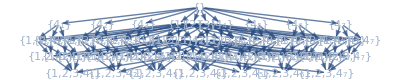

# twists | 0 | 1 | 2 | 3 | 4
# functions | 1 | 10 | 24 | 22 | 7

```mathematica
funcTree@list
```

#### Twist replacements

Replacement operations at each vertex:

```mathematica
rr[1][f_]:=replace[1,12]@f
rr[2][f_]:=replace[2,13]@f
rr[3][f_]:=replace[3,14]@f

rr[Subscript[4, 1]][f_]:=replace[{4,7,8,11},15]@f-replace[{4,6,7,8,9,11},15]@f-replace[{4,6,7,8,10,11},15]@f+replace[{4,6,7,8,9,10,11},15]@f
rr[Subscript[4, 2]][f_]:=replace[{4,6,8,10},15]@f-replace[{4,6,7,8,9,10},15]@f-replace[{4,6,7,8,10,11},15]@f+replace[{4,6,7,8,9,10,11},15]@f
rr[Subscript[4, 3]][f_]:=replace[{4,6,7,9},15]@f-replace[{4,6,7,8,9,10},15]@f-replace[{4,6,7,8,9,11},15]@f+replace[{4,6,7,8,9,10,11},15]@f
rr[Subscript[4, 4]][f_]:=replace[{4,6,7,8,10,11},15]@f-replace[{4,6,7,8,9,10,11},15]@f
rr[Subscript[4, 5]][f_]:=replace[{4,6,7,8,9,10},15]@f-replace[{4,6,7,8,9,10,11},15]@f
rr[Subscript[4, 6]][f_]:=replace[{4,6,7,8,9,11},15]@f-replace[{4,6,7,8,9,10,11},15]@f
rr[Subscript[4, 7]][f_]:=replace[{4,6,7,8,9,10,11},15]@f
```

Wavefunction:

```mathematica
ψ=-⟨1,2,3,4⟩+⟨1,2,3,5⟩+⟨1,2,3,6⟩+⟨1,2,3,7⟩+⟨1,2,3,8⟩-⟨1,2,3,9⟩-⟨1,2,3,10⟩-⟨1,2,3,11⟩-⟨1,2,4,8⟩+⟨1,2,5,9⟩+⟨1,2,6,10⟩+⟨1,2,7,11⟩+⟨1,3,4,7⟩-⟨1,3,5,10⟩-⟨1,3,6,9⟩-⟨1,3,8,11⟩-⟨1,4,7,11⟩+⟨1,4,8,11⟩+⟨1,5,6,9⟩-⟨1,5,6,10⟩-⟨2,3,4,6⟩+⟨2,3,5,11⟩+⟨2,3,7,9⟩+⟨2,3,8,10⟩+⟨2,4,6,10⟩-⟨2,4,8,10⟩-⟨2,5,7,9⟩+⟨2,5,7,11⟩-⟨3,4,6,9⟩+⟨3,4,7,9⟩+⟨3,5,8,10⟩-⟨3,5,8,11⟩-⟨4,5,6,9⟩+⟨4,5,6,10⟩+⟨4,5,7,9⟩-⟨4,5,7,11⟩-⟨4,5,8,10⟩+⟨4,5,8,11⟩;
```

Generate basis functions:

```mathematica
Subscript[f, {}]==(Subscript[F, {}]=ψ);

Table[Subscript[f, nn[[2]][[j]]]==(Subscript[F, nn[[2]][[j]]]=ψ//rr[nn[[2]][[j]][[1]]]),{j,Length@nn[[2]]}]//Column;

Table[Subscript[f, nn[[3]][[j]]]==(Subscript[F, nn[[3]][[j]]]=ψ//rr[nn[[3]][[j]][[1]]]//rr[nn[[3]][[j]][[2]]]),{j,Length@nn[[3]]}]//Column;

Table[Subscript[f, nn[[4]][[j]]]==(Subscript[F, nn[[4]][[j]]]=ψ//rr[nn[[4]][[j]][[1]]]//rr[nn[[4]][[j]][[2]]]//rr[nn[[4]][[j]][[3]]]),{j,Length@nn[[4]]}]//Column;

Table[Subscript[f, nn[[5]][[j]]]==(Subscript[F, nn[[5]][[j]]]=ψ//rr[nn[[5]][[j]][[1]]]//rr[nn[[5]][[j]][[2]]]//rr[nn[[5]][[j]][[3]]]//rr[nn[[5]][[j]][[4]]]),{j,Length@nn[[5]]}]//Column;
```

### Differential equations

```mathematica
solveCoeff;//AbsoluteTiming
```

{30.7889,Null}

#### Level 1

```mathematica
eqlvl[1]//Column
```

d[f_{}]==dL_(X1+Y14) (f_{}-f_{1})+dL_(X1-Y14) f_{1}+dL_(X2+Y24) (f_{}-f_{2})+dL_(X2-Y24) f_{2}+dL_(X3+Y34) (f_{}-f_{3})+dL_(X3-Y34) f_{3}+dL_(X4-Y14+Y24+Y34) f_{4_1}+dL_(X4+Y14-Y24+Y34) f_{4_2}+dL_(X4+Y14+Y24-Y34) f_{4_3}+dL_(X4-Y14-Y24+Y34) f_{4_4}+dL_(X4+Y14-Y24-Y34) f_{4_5}+dL_(X4-Y14+Y24-Y34) f_{4_6}+dL_(X4+Y14+Y24+Y34) (f_{}-f_{4_1}-f_{4_2}-f_{4_3}-f_{4_4}-f_{4_5}-f_{4_6}-f_{4_7})+dL_(X4-Y14-Y24-Y34) f_{4_7}

#### Level 2

```mathematica
eqlvl[2]//Column
```

d[f_{1}]==dL_(X1-Y14) f_{1}+dL_(X2+Y24) (f_{1}-f_{1,2})+dL_(X2-Y24) f_{1,2}+dL_(X3+Y34) (f_{1}-f_{1,3})+dL_(X3-Y34) f_{1,3}+dL_(X1+X4+Y24+Y34) f_{1,4_1}+dL_(X4+Y14-Y24+Y34) f_{1,4_2}+dL_(X4+Y14+Y24-Y34) f_{1,4_3}+dL_(X1+X4-Y24+Y34) f_{1,4_4}+dL_(X4+Y14-Y24-Y34) f_{1,4_5}+dL_(X1+X4+Y24-Y34) f_{1,4_6}+dL_(X4+Y14+Y24+Y34) (f_{1}-f_{1,4_1}-f_{1,4_2}-f_{1,4_3}-f_{1,4_4}-f_{1,4_5}-f_{1,4_6}-f_{1,4_7})+dL_(X1+X4-Y24-Y34) f_{1,4_7}
d[f_{2}]==dL_(X2-Y24) f_{2}+dL_(X1+Y14) (f_{2}-f_{1,2})+dL_(X1-Y14) f_{1,2}+dL_(X3+Y34) (f_{2}-f_{2,3})+dL_(X3-Y34) f_{2,3}+dL_(X4-Y14+Y24+Y34) f_{2,4_1}+dL_(X2+X4+Y14+Y34) f_{2,4_2}+dL_(X4+Y14+Y24-Y34) f_{2,4_3}+dL_(X2+X4-Y14+Y34) f_{2,4_4}+dL_(X2+X4+Y14-Y34) f_{2,4_5}+dL_(X4-Y14+Y24-Y34) f_{2,4_6}+dL_(X4+Y14+Y24+Y34) (f_{2}-f_{2,4_1}-f_{2,4_2}-f_{2,4_3}-f_{2,4_4}-f_{2,4_5}-f_{2,4_6}-f_{2,4_7})+dL_(X2+X4-Y14-Y34) f_{2,4_7}
d[f_{3}]==dL_(X3-Y34) f_{3}+dL_(X1+Y14) (f_{3}-f_{1,3})+dL_(X1-Y14) f_{1,3}+dL_(X2+Y24) (f_{3}-f_{2,3})+dL_(X2-Y24) f_{2,3}+dL_(X4-Y14+Y24+Y34) f_{3,4_1}+dL_(X4+Y14-Y24+Y34) f_{3,4_2}+dL_(X3+X4+Y14+Y24) f_{3,4_3}+dL_(X4-Y14-Y24+Y34) f_{3,4_4}+dL_(X3+X4+Y14-Y24) f_{3,4_5}+dL_(X3+X4-Y14+Y24) f_{3,4_6}+dL_(X4+Y14+Y24+Y34) (f_{3}-f_{3,4_1}-f_{3,4_2}-f_{3,4_3}-f_{3,4_4}-f_{3,4_5}-f_{3,4_6}-f_{3,4_7})+dL_(X3+X4-Y14-Y24) f_{3,4_7}
d[f_{4_1}]==dL_(X4-Y14+Y24+Y34) f_{4_1}+dL_(X1+Y14) (f_{4_1}-f_{1,4_1})+dL_(X1+X4+Y24+Y34) f_{1,4_1}+dL_(X2+Y24) (f_{4_1}-f_{2,4_1})-dL_(X2+X4-Y14+Y34) f_{2,4_4}+dL_(X2-Y24) (f_{2,4_1}+f_{2,4_4})+dL_(X3+Y34) (f_{4_1}-f_{3,4_1})-dL_(X3+X4-Y14+Y24) f_{3,4_6}+dL_(X3-Y34) (f_{3,4_1}+f_{3,4_6})
d[f_{4_2}]==dL_(X4+Y14-Y24+Y34) f_{4_2}+dL_(X1+Y14) (f_{4_2}-f_{1,4_2})-dL_(X1+X4-Y24+Y34) f_{1,4_4}+dL_(X1-Y14) (f_{1,4_2}+f_{1,4_4})+dL_(X2+Y24) (f_{4_2}-f_{2,4_2})+dL_(X2+X4+Y14+Y34) f_{2,4_2}+dL_(X3+Y34) (f_{4_2}-f_{3,4_2})-dL_(X3+X4+Y14-Y24) f_{3,4_5}+dL_(X3-Y34) (f_{3,4_2}+f_{3,4_5})
d[f_{4_3}]==dL_(X4+Y14+Y24-Y34) f_{4_3}+dL_(X1+Y14) (f_{4_3}-f_{1,4_3})-dL_(X1+X4+Y24-Y34) f_{1,4_6}+dL_(X1-Y14) (f_{1,4_3}+f_{1,4_6})+dL_(X2+Y24) (f_{4_3}-f_{2,4_3})-dL_(X2+X4+Y14-Y34) f_{2,4_5}+dL_(X2-Y24) (f_{2,4_3}+f_{2,4_5})+dL_(X3+Y34) (f_{4_3}-f_{3,4_3})+dL_(X3+X4+Y14+Y24) f_{3,4_3}
d[f_{4_4}]==dL_(X4-Y14-Y24+Y34) f_{4_4}+dL_(X1+Y14) (f_{4_4}-f_{1,4_4})+dL_(X1+X4-Y24+Y34) f_{1,4_4}+dL_(X2+Y24) (f_{4_4}-f_{2,4_4})+dL_(X2+X4-Y14+Y34) f_{2,4_4}+dL_(X3+Y34) (f_{4_4}-f_{3,4_4})-dL_(X3+X4-Y14-Y24) f_{3,4_7}+dL_(X3-Y34) (f_{3,4_4}+f_{3,4_7})
d[f_{4_5}]==dL_(X4+Y14-Y24-Y34) f_{4_5}+dL_(X1+Y14) (f_{4_5}-f_{1,4_5})-dL_(X1+X4-Y24-Y34) f_{1,4_7}+dL_(X1-Y14) (f_{1,4_5}+f_{1,4_7})+dL_(X2+Y24) (f_{4_5}-f_{2,4_5})+dL_(X2+X4+Y14-Y34) f_{2,4_5}+dL_(X3+Y34) (f_{4_5}-f_{3,4_5})+dL_(X3+X4+Y14-Y24) f_{3,4_5}
d[f_{4_6}]==dL_(X4-Y14+Y24-Y34) f_{4_6}+dL_(X1+Y14) (f_{4_6}-f_{1,4_6})+dL_(X1+X4+Y24-Y34) f_{1,4_6}+dL_(X2+Y24) (f_{4_6}-f_{2,4_6})-dL_(X2+X4-Y14-Y34) f_{2,4_7}+dL_(X2-Y24) (f_{2,4_6}+f_{2,4_7})+dL_(X3+Y34) (f_{4_6}-f_{3,4_6})+dL_(X3+X4-Y14+Y24) f_{3,4_6}
d[f_{4_7}]==dL_(X4-Y14-Y24-Y34) f_{4_7}+dL_(X1+Y14) (f_{4_7}-f_{1,4_7})+dL_(X1+X4-Y24-Y34) f_{1,4_7}+dL_(X2+Y24) (f_{4_7}-f_{2,4_7})+dL_(X2+X4-Y14-Y34) f_{2,4_7}+dL_(X3+Y34) (f_{4_7}-f_{3,4_7})+dL_(X3+X4-Y14-Y24) f_{3,4_7}

#### Level 3

```mathematica
eqlvl[3]//Column
```

d[f_{1,2}]==dL_(X1-Y14) f_{1,2}+dL_(X2-Y24) f_{1,2}+dL_(X3+Y34) (f_{1,2}-f_{1,2,3})+dL_(X3-Y34) f_{1,2,3}+dL_(X1+X4+Y24+Y34) f_{1,2,4_1}+dL_(X2+X4+Y14+Y34) f_{1,2,4_2}+dL_(X4+Y14+Y24-Y34) f_{1,2,4_3}+dL_(X1+X2+X4+Y34) f_{1,2,4_4}+dL_(X2+X4+Y14-Y34) f_{1,2,4_5}+dL_(X1+X4+Y24-Y34) f_{1,2,4_6}+dL_(X4+Y14+Y24+Y34) (f_{1,2}-f_{1,2,4_1}-f_{1,2,4_2}-f_{1,2,4_3}-f_{1,2,4_4}-f_{1,2,4_5}-f_{1,2,4_6}-f_{1,2,4_7})+dL_(X1+X2+X4-Y34) f_{1,2,4_7}
d[f_{1,3}]==dL_(X1-Y14) f_{1,3}+dL_(X3-Y34) f_{1,3}+dL_(X2+Y24) (f_{1,3}-f_{1,2,3})+dL_(X2-Y24) f_{1,2,3}+dL_(X1+X4+Y24+Y34) f_{1,3,4_1}+dL_(X4+Y14-Y24+Y34) f_{1,3,4_2}+dL_(X3+X4+Y14+Y24) f_{1,3,4_3}+dL_(X1+X4-Y24+Y34) f_{1,3,4_4}+dL_(X3+X4+Y14-Y24) f_{1,3,4_5}+dL_(X1+X3+X4+Y24) f_{1,3,4_6}+dL_(X4+Y14+Y24+Y34) (f_{1,3}-f_{1,3,4_1}-f_{1,3,4_2}-f_{1,3,4_3}-f_{1,3,4_4}-f_{1,3,4_5}-f_{1,3,4_6}-f_{1,3,4_7})+dL_(X1+X3+X4-Y24) f_{1,3,4_7}
d[f_{1,4_1}]==2 dL_(X1+X4+Y24+Y34) f_{1,4_1}+dL_(X2+Y24) (f_{1,4_1}-f_{1,2,4_1})-dL_(X1+X2+X4+Y34) f_{1,2,4_4}+dL_(X2-Y24) (f_{1,2,4_1}+f_{1,2,4_4})+dL_(X3+Y34) (f_{1,4_1}-f_{1,3,4_1})-dL_(X1+X3+X4+Y24) f_{1,3,4_6}+dL_(X3-Y34) (f_{1,3,4_1}+f_{1,3,4_6})
d[f_{1,4_2}]==dL_(X4+Y14-Y24+Y34) f_{1,4_2}-dL_(X1+X4-Y24+Y34) f_{1,4_4}+dL_(X1-Y14) (f_{1,4_2}+f_{1,4_4})+dL_(X2+Y24) (f_{1,4_2}-f_{1,2,4_2})+dL_(X2+X4+Y14+Y34) f_{1,2,4_2}+dL_(X3+Y34) (f_{1,4_2}-f_{1,3,4_2})-dL_(X3+X4+Y14-Y24) f_{1,3,4_5}+dL_(X3-Y34) (f_{1,3,4_2}+f_{1,3,4_5})
d[f_{1,4_3}]==dL_(X4+Y14+Y24-Y34) f_{1,4_3}-dL_(X1+X4+Y24-Y34) f_{1,4_6}+dL_(X1-Y14) (f_{1,4_3}+f_{1,4_6})+dL_(X2+Y24) (f_{1,4_3}-f_{1,2,4_3})-dL_(X2+X4+Y14-Y34) f_{1,2,4_5}+dL_(X2-Y24) (f_{1,2,4_3}+f_{1,2,4_5})+dL_(X3+Y34) (f_{1,4_3}-f_{1,3,4_3})+dL_(X3+X4+Y14+Y24) f_{1,3,4_3}
d[f_{1,4_4}]==2 dL_(X1+X4-Y24+Y34) f_{1,4_4}+dL_(X2+Y24) (f_{1,4_4}-f_{1,2,4_4})+dL_(X1+X2+X4+Y34) f_{1,2,4_4}+dL_(X3+Y34) (f_{1,4_4}-f_{1,3,4_4})-dL_(X1+X3+X4-Y24) f_{1,3,4_7}+dL_(X3-Y34) (f_{1,3,4_4}+f_{1,3,4_7})
d[f_{1,4_5}]==dL_(X4+Y14-Y24-Y34) f_{1,4_5}-dL_(X1+X4-Y24-Y34) f_{1,4_7}+dL_(X1-Y14) (f_{1,4_5}+f_{1,4_7})+dL_(X2+Y24) (f_{1,4_5}-f_{1,2,4_5})+dL_(X2+X4+Y14-Y34) f_{1,2,4_5}+dL_(X3+Y34) (f_{1,4_5}-f_{1,3,4_5})+dL_(X3+X4+Y14-Y24) f_{1,3,4_5}
d[f_{1,4_6}]==2 dL_(X1+X4+Y24-Y34) f_{1,4_6}+dL_(X2+Y24) (f_{1,4_6}-f_{1,2,4_6})-dL_(X1+X2+X4-Y34) f_{1,2,4_7}+dL_(X2-Y24) (f_{1,2,4_6}+f_{1,2,4_7})+dL_(X3+Y34) (f_{1,4_6}-f_{1,3,4_6})+dL_(X1+X3+X4+Y24) f_{1,3,4_6}
d[f_{1,4_7}]==2 dL_(X1+X4-Y24-Y34) f_{1,4_7}+dL_(X2+Y24) (f_{1,4_7}-f_{1,2,4_7})+dL_(X1+X2+X4-Y34) f_{1,2,4_7}+dL_(X3+Y34) (f_{1,4_7}-f_{1,3,4_7})+dL_(X1+X3+X4-Y24) f_{1,3,4_7}
d[f_{2,3}]==dL_(X2-Y24) f_{2,3}+dL_(X3-Y34) f_{2,3}+dL_(X1+Y14) (f_{2,3}-f_{1,2,3})+dL_(X1-Y14) f_{1,2,3}+dL_(X4-Y14+Y24+Y34) f_{2,3,4_1}+dL_(X2+X4+Y14+Y34) f_{2,3,4_2}+dL_(X3+X4+Y14+Y24) f_{2,3,4_3}+dL_(X2+X4-Y14+Y34) f_{2,3,4_4}+dL_(X2+X3+X4+Y14) f_{2,3,4_5}+dL_(X3+X4-Y14+Y24) f_{2,3,4_6}+dL_(X4+Y14+Y24+Y34) (f_{2,3}-f_{2,3,4_1}-f_{2,3,4_2}-f_{2,3,4_3}-f_{2,3,4_4}-f_{2,3,4_5}-f_{2,3,4_6}-f_{2,3,4_7})+dL_(X2+X3+X4-Y14) f_{2,3,4_7}
d[f_{2,4_1}]==dL_(X4-Y14+Y24+Y34) f_{2,4_1}-dL_(X2+X4-Y14+Y34) f_{2,4_4}+dL_(X2-Y24) (f_{2,4_1}+f_{2,4_4})+dL_(X1+Y14) (f_{2,4_1}-f_{1,2,4_1})+dL_(X1+X4+Y24+Y34) f_{1,2,4_1}+dL_(X3+Y34) (f_{2,4_1}-f_{2,3,4_1})-dL_(X3+X4-Y14+Y24) f_{2,3,4_6}+dL_(X3-Y34) (f_{2,3,4_1}+f_{2,3,4_6})
d[f_{2,4_2}]==2 dL_(X2+X4+Y14+Y34) f_{2,4_2}+dL_(X1+Y14) (f_{2,4_2}-f_{1,2,4_2})-dL_(X1+X2+X4+Y34) f_{1,2,4_4}+dL_(X1-Y14) (f_{1,2,4_2}+f_{1,2,4_4})+dL_(X3+Y34) (f_{2,4_2}-f_{2,3,4_2})-dL_(X2+X3+X4+Y14) f_{2,3,4_5}+dL_(X3-Y34) (f_{2,3,4_2}+f_{2,3,4_5})
d[f_{2,4_3}]==dL_(X4+Y14+Y24-Y34) f_{2,4_3}-dL_(X2+X4+Y14-Y34) f_{2,4_5}+dL_(X2-Y24) (f_{2,4_3}+f_{2,4_5})+dL_(X1+Y14) (f_{2,4_3}-f_{1,2,4_3})-dL_(X1+X4+Y24-Y34) f_{1,2,4_6}+dL_(X1-Y14) (f_{1,2,4_3}+f_{1,2,4_6})+dL_(X3+Y34) (f_{2,4_3}-f_{2,3,4_3})+dL_(X3+X4+Y14+Y24) f_{2,3,4_3}
d[f_{2,4_4}]==2 dL_(X2+X4-Y14+Y34) f_{2,4_4}+dL_(X1+Y14) (f_{2,4_4}-f_{1,2,4_4})+dL_(X1+X2+X4+Y34) f_{1,2,4_4}+dL_(X3+Y34) (f_{2,4_4}-f_{2,3,4_4})-dL_(X2+X3+X4-Y14) f_{2,3,4_7}+dL_(X3-Y34) (f_{2,3,4_4}+f_{2,3,4_7})
d[f_{2,4_5}]==2 dL_(X2+X4+Y14-Y34) f_{2,4_5}+dL_(X1+Y14) (f_{2,4_5}-f_{1,2,4_5})-dL_(X1+X2+X4-Y34) f_{1,2,4_7}+dL_(X1-Y14) (f_{1,2,4_5}+f_{1,2,4_7})+dL_(X3+Y34) (f_{2,4_5}-f_{2,3,4_5})+dL_(X2+X3+X4+Y14) f_{2,3,4_5}
d[f_{2,4_6}]==dL_(X4-Y14+Y24-Y34) f_{2,4_6}-dL_(X2+X4-Y14-Y34) f_{2,4_7}+dL_(X2-Y24) (f_{2,4_6}+f_{2,4_7})+dL_(X1+Y14) (f_{2,4_6}-f_{1,2,4_6})+dL_(X1+X4+Y24-Y34) f_{1,2,4_6}+dL_(X3+Y34) (f_{2,4_6}-f_{2,3,4_6})+dL_(X3+X4-Y14+Y24) f_{2,3,4_6}
d[f_{2,4_7}]==2 dL_(X2+X4-Y14-Y34) f_{2,4_7}+dL_(X1+Y14) (f_{2,4_7}-f_{1,2,4_7})+dL_(X1+X2+X4-Y34) f_{1,2,4_7}+dL_(X3+Y34) (f_{2,4_7}-f_{2,3,4_7})+dL_(X2+X3+X4-Y14) f_{2,3,4_7}
d[f_{3,4_1}]==dL_(X4-Y14+Y24+Y34) f_{3,4_1}-dL_(X3+X4-Y14+Y24) f_{3,4_6}+dL_(X3-Y34) (f_{3,4_1}+f_{3,4_6})+dL_(X1+Y14) (f_{3,4_1}-f_{1,3,4_1})+dL_(X1+X4+Y24+Y34) f_{1,3,4_1}+dL_(X2+Y24) (f_{3,4_1}-f_{2,3,4_1})-dL_(X2+X4-Y14+Y34) f_{2,3,4_4}+dL_(X2-Y24) (f_{2,3,4_1}+f_{2,3,4_4})
d[f_{3,4_2}]==dL_(X4+Y14-Y24+Y34) f_{3,4_2}-dL_(X3+X4+Y14-Y24) f_{3,4_5}+dL_(X3-Y34) (f_{3,4_2}+f_{3,4_5})+dL_(X1+Y14) (f_{3,4_2}-f_{1,3,4_2})-dL_(X1+X4-Y24+Y34) f_{1,3,4_4}+dL_(X1-Y14) (f_{1,3,4_2}+f_{1,3,4_4})+dL_(X2+Y24) (f_{3,4_2}-f_{2,3,4_2})+dL_(X2+X4+Y14+Y34) f_{2,3,4_2}
d[f_{3,4_3}]==2 dL_(X3+X4+Y14+Y24) f_{3,4_3}+dL_(X1+Y14) (f_{3,4_3}-f_{1,3,4_3})-dL_(X1+X3+X4+Y24) f_{1,3,4_6}+dL_(X1-Y14) (f_{1,3,4_3}+f_{1,3,4_6})+dL_(X2+Y24) (f_{3,4_3}-f_{2,3,4_3})-dL_(X2+X3+X4+Y14) f_{2,3,4_5}+dL_(X2-Y24) (f_{2,3,4_3}+f_{2,3,4_5})
d[f_{3,4_4}]==dL_(X4-Y14-Y24+Y34) f_{3,4_4}-dL_(X3+X4-Y14-Y24) f_{3,4_7}+dL_(X3-Y34) (f_{3,4_4}+f_{3,4_7})+dL_(X1+Y14) (f_{3,4_4}-f_{1,3,4_4})+dL_(X1+X4-Y24+Y34) f_{1,3,4_4}+dL_(X2+Y24) (f_{3,4_4}-f_{2,3,4_4})+dL_(X2+X4-Y14+Y34) f_{2,3,4_4}
d[f_{3,4_5}]==2 dL_(X3+X4+Y14-Y24) f_{3,4_5}+dL_(X1+Y14) (f_{3,4_5}-f_{1,3,4_5})-dL_(X1+X3+X4-Y24) f_{1,3,4_7}+dL_(X1-Y14) (f_{1,3,4_5}+f_{1,3,4_7})+dL_(X2+Y24) (f_{3,4_5}-f_{2,3,4_5})+dL_(X2+X3+X4+Y14) f_{2,3,4_5}
d[f_{3,4_6}]==2 dL_(X3+X4-Y14+Y24) f_{3,4_6}+dL_(X1+Y14) (f_{3,4_6}-f_{1,3,4_6})+dL_(X1+X3+X4+Y24) f_{1,3,4_6}+dL_(X2+Y24) (f_{3,4_6}-f_{2,3,4_6})-dL_(X2+X3+X4-Y14) f_{2,3,4_7}+dL_(X2-Y24) (f_{2,3,4_6}+f_{2,3,4_7})
d[f_{3,4_7}]==2 dL_(X3+X4-Y14-Y24) f_{3,4_7}+dL_(X1+Y14) (f_{3,4_7}-f_{1,3,4_7})+dL_(X1+X3+X4-Y24) f_{1,3,4_7}+dL_(X2+Y24) (f_{3,4_7}-f_{2,3,4_7})+dL_(X2+X3+X4-Y14) f_{2,3,4_7}

#### Level 4

```mathematica
eqlvl[4]//Column
```

d[f_{1,2,3}]==dL_(X1-Y14) f_{1,2,3}+dL_(X2-Y24) f_{1,2,3}+dL_(X3-Y34) f_{1,2,3}+dL_(X1+X4+Y24+Y34) f_{1,2,3,4_1}+dL_(X2+X4+Y14+Y34) f_{1,2,3,4_2}+dL_(X3+X4+Y14+Y24) f_{1,2,3,4_3}+dL_(X1+X2+X4+Y34) f_{1,2,3,4_4}+dL_(X2+X3+X4+Y14) f_{1,2,3,4_5}+dL_(X1+X3+X4+Y24) f_{1,2,3,4_6}+dL_(X4+Y14+Y24+Y34) (f_{1,2,3}-f_{1,2,3,4_1}-f_{1,2,3,4_2}-f_{1,2,3,4_3}-f_{1,2,3,4_4}-f_{1,2,3,4_5}-f_{1,2,3,4_6}-f_{1,2,3,4_7})+dL_(X1+X2+X3+X4) f_{1,2,3,4_7}
d[f_{1,2,4_1}]==2 dL_(X1+X4+Y24+Y34) f_{1,2,4_1}-dL_(X1+X2+X4+Y34) f_{1,2,4_4}+dL_(X2-Y24) (f_{1,2,4_1}+f_{1,2,4_4})+dL_(X3+Y34) (f_{1,2,4_1}-f_{1,2,3,4_1})-dL_(X1+X3+X4+Y24) f_{1,2,3,4_6}+dL_(X3-Y34) (f_{1,2,3,4_1}+f_{1,2,3,4_6})
d[f_{1,2,4_2}]==2 dL_(X2+X4+Y14+Y34) f_{1,2,4_2}-dL_(X1+X2+X4+Y34) f_{1,2,4_4}+dL_(X1-Y14) (f_{1,2,4_2}+f_{1,2,4_4})+dL_(X3+Y34) (f_{1,2,4_2}-f_{1,2,3,4_2})-dL_(X2+X3+X4+Y14) f_{1,2,3,4_5}+dL_(X3-Y34) (f_{1,2,3,4_2}+f_{1,2,3,4_5})
d[f_{1,2,4_3}]==dL_(X4+Y14+Y24-Y34) f_{1,2,4_3}-dL_(X2+X4+Y14-Y34) f_{1,2,4_5}+dL_(X2-Y24) (f_{1,2,4_3}+f_{1,2,4_5})-dL_(X1+X4+Y24-Y34) f_{1,2,4_6}+dL_(X1-Y14) (f_{1,2,4_3}+f_{1,2,4_6})+dL_(X3+Y34) (f_{1,2,4_3}-f_{1,2,3,4_3})+dL_(X3+X4+Y14+Y24) f_{1,2,3,4_3}
d[f_{1,2,4_4}]==3 dL_(X1+X2+X4+Y34) f_{1,2,4_4}+dL_(X3+Y34) (f_{1,2,4_4}-f_{1,2,3,4_4})-dL_(X1+X2+X3+X4) f_{1,2,3,4_7}+dL_(X3-Y34) (f_{1,2,3,4_4}+f_{1,2,3,4_7})
d[f_{1,2,4_5}]==2 dL_(X2+X4+Y14-Y34) f_{1,2,4_5}-dL_(X1+X2+X4-Y34) f_{1,2,4_7}+dL_(X1-Y14) (f_{1,2,4_5}+f_{1,2,4_7})+dL_(X3+Y34) (f_{1,2,4_5}-f_{1,2,3,4_5})+dL_(X2+X3+X4+Y14) f_{1,2,3,4_5}
d[f_{1,2,4_6}]==2 dL_(X1+X4+Y24-Y34) f_{1,2,4_6}-dL_(X1+X2+X4-Y34) f_{1,2,4_7}+dL_(X2-Y24) (f_{1,2,4_6}+f_{1,2,4_7})+dL_(X3+Y34) (f_{1,2,4_6}-f_{1,2,3,4_6})+dL_(X1+X3+X4+Y24) f_{1,2,3,4_6}
d[f_{1,2,4_7}]==3 dL_(X1+X2+X4-Y34) f_{1,2,4_7}+dL_(X3+Y34) (f_{1,2,4_7}-f_{1,2,3,4_7})+dL_(X1+X2+X3+X4) f_{1,2,3,4_7}
d[f_{1,3,4_1}]==2 dL_(X1+X4+Y24+Y34) f_{1,3,4_1}-dL_(X1+X3+X4+Y24) f_{1,3,4_6}+dL_(X3-Y34) (f_{1,3,4_1}+f_{1,3,4_6})+dL_(X2+Y24) (f_{1,3,4_1}-f_{1,2,3,4_1})-dL_(X1+X2+X4+Y34) f_{1,2,3,4_4}+dL_(X2-Y24) (f_{1,2,3,4_1}+f_{1,2,3,4_4})
d[f_{1,3,4_2}]==dL_(X4+Y14-Y24+Y34) f_{1,3,4_2}-dL_(X1+X4-Y24+Y34) f_{1,3,4_4}+dL_(X1-Y14) (f_{1,3,4_2}+f_{1,3,4_4})-dL_(X3+X4+Y14-Y24) f_{1,3,4_5}+dL_(X3-Y34) (f_{1,3,4_2}+f_{1,3,4_5})+dL_(X2+Y24) (f_{1,3,4_2}-f_{1,2,3,4_2})+dL_(X2+X4+Y14+Y34) f_{1,2,3,4_2}
d[f_{1,3,4_3}]==2 dL_(X3+X4+Y14+Y24) f_{1,3,4_3}-dL_(X1+X3+X4+Y24) f_{1,3,4_6}+dL_(X1-Y14) (f_{1,3,4_3}+f_{1,3,4_6})+dL_(X2+Y24) (f_{1,3,4_3}-f_{1,2,3,4_3})-dL_(X2+X3+X4+Y14) f_{1,2,3,4_5}+dL_(X2-Y24) (f_{1,2,3,4_3}+f_{1,2,3,4_5})
d[f_{1,3,4_4}]==2 dL_(X1+X4-Y24+Y34) f_{1,3,4_4}-dL_(X1+X3+X4-Y24) f_{1,3,4_7}+dL_(X3-Y34) (f_{1,3,4_4}+f_{1,3,4_7})+dL_(X2+Y24) (f_{1,3,4_4}-f_{1,2,3,4_4})+dL_(X1+X2+X4+Y34) f_{1,2,3,4_4}
d[f_{1,3,4_5}]==2 dL_(X3+X4+Y14-Y24) f_{1,3,4_5}-dL_(X1+X3+X4-Y24) f_{1,3,4_7}+dL_(X1-Y14) (f_{1,3,4_5}+f_{1,3,4_7})+dL_(X2+Y24) (f_{1,3,4_5}-f_{1,2,3,4_5})+dL_(X2+X3+X4+Y14) f_{1,2,3,4_5}
d[f_{1,3,4_6}]==3 dL_(X1+X3+X4+Y24) f_{1,3,4_6}+dL_(X2+Y24) (f_{1,3,4_6}-f_{1,2,3,4_6})-dL_(X1+X2+X3+X4) f_{1,2,3,4_7}+dL_(X2-Y24) (f_{1,2,3,4_6}+f_{1,2,3,4_7})
d[f_{1,3,4_7}]==3 dL_(X1+X3+X4-Y24) f_{1,3,4_7}+dL_(X2+Y24) (f_{1,3,4_7}-f_{1,2,3,4_7})+dL_(X1+X2+X3+X4) f_{1,2,3,4_7}
d[f_{2,3,4_1}]==dL_(X4-Y14+Y24+Y34) f_{2,3,4_1}-dL_(X2+X4-Y14+Y34) f_{2,3,4_4}+dL_(X2-Y24) (f_{2,3,4_1}+f_{2,3,4_4})-dL_(X3+X4-Y14+Y24) f_{2,3,4_6}+dL_(X3-Y34) (f_{2,3,4_1}+f_{2,3,4_6})+dL_(X1+Y14) (f_{2,3,4_1}-f_{1,2,3,4_1})+dL_(X1+X4+Y24+Y34) f_{1,2,3,4_1}
d[f_{2,3,4_2}]==2 dL_(X2+X4+Y14+Y34) f_{2,3,4_2}-dL_(X2+X3+X4+Y14) f_{2,3,4_5}+dL_(X3-Y34) (f_{2,3,4_2}+f_{2,3,4_5})+dL_(X1+Y14) (f_{2,3,4_2}-f_{1,2,3,4_2})-dL_(X1+X2+X4+Y34) f_{1,2,3,4_4}+dL_(X1-Y14) (f_{1,2,3,4_2}+f_{1,2,3,4_4})
d[f_{2,3,4_3}]==2 dL_(X3+X4+Y14+Y24) f_{2,3,4_3}-dL_(X2+X3+X4+Y14) f_{2,3,4_5}+dL_(X2-Y24) (f_{2,3,4_3}+f_{2,3,4_5})+dL_(X1+Y14) (f_{2,3,4_3}-f_{1,2,3,4_3})-dL_(X1+X3+X4+Y24) f_{1,2,3,4_6}+dL_(X1-Y14) (f_{1,2,3,4_3}+f_{1,2,3,4_6})
d[f_{2,3,4_4}]==2 dL_(X2+X4-Y14+Y34) f_{2,3,4_4}-dL_(X2+X3+X4-Y14) f_{2,3,4_7}+dL_(X3-Y34) (f_{2,3,4_4}+f_{2,3,4_7})+dL_(X1+Y14) (f_{2,3,4_4}-f_{1,2,3,4_4})+dL_(X1+X2+X4+Y34) f_{1,2,3,4_4}
d[f_{2,3,4_5}]==3 dL_(X2+X3+X4+Y14) f_{2,3,4_5}+dL_(X1+Y14) (f_{2,3,4_5}-f_{1,2,3,4_5})-dL_(X1+X2+X3+X4) f_{1,2,3,4_7}+dL_(X1-Y14) (f_{1,2,3,4_5}+f_{1,2,3,4_7})
d[f_{2,3,4_6}]==2 dL_(X3+X4-Y14+Y24) f_{2,3,4_6}-dL_(X2+X3+X4-Y14) f_{2,3,4_7}+dL_(X2-Y24) (f_{2,3,4_6}+f_{2,3,4_7})+dL_(X1+Y14) (f_{2,3,4_6}-f_{1,2,3,4_6})+dL_(X1+X3+X4+Y24) f_{1,2,3,4_6}
d[f_{2,3,4_7}]==3 dL_(X2+X3+X4-Y14) f_{2,3,4_7}+dL_(X1+Y14) (f_{2,3,4_7}-f_{1,2,3,4_7})+dL_(X1+X2+X3+X4) f_{1,2,3,4_7}

#### Level 5

```mathematica
eqlvl[5]//Column
```

d[f_{1,2,3,4_1}]==2 dL_(X1+X4+Y24+Y34) f_{1,2,3,4_1}-dL_(X1+X2+X4+Y34) f_{1,2,3,4_4}+dL_(X2-Y24) (f_{1,2,3,4_1}+f_{1,2,3,4_4})-dL_(X1+X3+X4+Y24) f_{1,2,3,4_6}+dL_(X3-Y34) (f_{1,2,3,4_1}+f_{1,2,3,4_6})
d[f_{1,2,3,4_2}]==2 dL_(X2+X4+Y14+Y34) f_{1,2,3,4_2}-dL_(X1+X2+X4+Y34) f_{1,2,3,4_4}+dL_(X1-Y14) (f_{1,2,3,4_2}+f_{1,2,3,4_4})-dL_(X2+X3+X4+Y14) f_{1,2,3,4_5}+dL_(X3-Y34) (f_{1,2,3,4_2}+f_{1,2,3,4_5})
d[f_{1,2,3,4_3}]==2 dL_(X3+X4+Y14+Y24) f_{1,2,3,4_3}-dL_(X2+X3+X4+Y14) f_{1,2,3,4_5}+dL_(X2-Y24) (f_{1,2,3,4_3}+f_{1,2,3,4_5})-dL_(X1+X3+X4+Y24) f_{1,2,3,4_6}+dL_(X1-Y14) (f_{1,2,3,4_3}+f_{1,2,3,4_6})
d[f_{1,2,3,4_4}]==3 dL_(X1+X2+X4+Y34) f_{1,2,3,4_4}-dL_(X1+X2+X3+X4) f_{1,2,3,4_7}+dL_(X3-Y34) (f_{1,2,3,4_4}+f_{1,2,3,4_7})
d[f_{1,2,3,4_5}]==3 dL_(X2+X3+X4+Y14) f_{1,2,3,4_5}-dL_(X1+X2+X3+X4) f_{1,2,3,4_7}+dL_(X1-Y14) (f_{1,2,3,4_5}+f_{1,2,3,4_7})
d[f_{1,2,3,4_6}]==3 dL_(X1+X3+X4+Y24) f_{1,2,3,4_6}-dL_(X1+X2+X3+X4) f_{1,2,3,4_7}+dL_(X2-Y24) (f_{1,2,3,4_6}+f_{1,2,3,4_7})
d[f_{1,2,3,4_7}]==4 dL_(X1+X2+X3+X4) f_{1,2,3,4_7}

### A matrix

```mathematica
flist=Flatten[Table[Subscript[f, nn[[l]][[m]]],{l,nsite+1},{m,Length@nn[[l]]}],1];
```

```mathematica
Flatten[Table[eqlvl[i][[m]][[2]],{i,0,nsite+1},{m,Length@eqlvl[i]}],1];
Amtx=Table[Coefficient[%[[i]],flist],{i,4^(nsite-1)}];
```

Check flatness:

```mathematica
A=Amtx/.Subscript[dL, a_]:>Dt@Log[a];
vars={X1,X2,X3,X4,Y14,Y24,Y34};
DeleteDuplicates@Flatten@Table[Coefficient[A,Dt[vars[[i]]]].Coefficient[A,Dt[vars[[j]]]]-Coefficient[A,Dt[vars[[j]]]].Coefficient[A,Dt[vars[[i]]]]//Simplify,{i,Length@vars},{j,Length@vars}]
```

{0}

### d^2=0

Three-letter relations:

```mathematica
DeleteDuplicates@DeleteCases[Flatten[Table[If[(-letters[[i]]+letters[[j]]+letters[[k]]//Simplify)===0∧i=!=j∧i=!=k∧j=!=k,{i,j,k},0],{i,Length@letters},{j,Length@letters},{k,Length@letters}],2],0];
reltab=Subscript[dL, letters[[#1]]]⋀Subscript[dL, letters[[#3]]]+Subscript[dL, letters[[#2]]]⋀Subscript[dL, letters[[#1]]]-Subscript[dL, letters[[#2]]]⋀Subscript[dL, letters[[#3]]]&@@@%//dLsimp;
```

Independent relations:

```mathematica
dLrel=Table[If[reltab[[i,1]][[1]]===-1,-reltab[[i]],reltab[[i]]],{i,Length@reltab}]//DeleteDuplicates;
dLsub=Table[%[[i]][[1]]->Subscript[R, i]-%[[i]][[2]]-%[[i]][[3]],{i,Length@%}];
%//Length
```

54

Taking d^2:

```mathematica
dfeq=Flatten@Table[eqlvl[l][[m]],{l,5},{m,Length@nn[[l]]}];
dfsub=dfeq/.a_==b_:>a->b;
ddeq=Flatten@Table[d[Subscript[f, nn[[l]][[m]]]],{l,5},{m,Length@nn[[l]]}]/.d[f_]:>(d^2)[f]==dd[f];
```

```mathematica
ddeq/.dLsub/.Subscript[R, _]->0//Simplify
```

{d^2[f_{}]==0,d^2[f_{1}]==0,d^2[f_{2}]==0,d^2[f_{3}]==0,d^2[f_{4_1}]==0,d^2[f_{4_2}]==0,d^2[f_{4_3}]==0,d^2[f_{4_4}]==0,d^2[f_{4_5}]==0,d^2[f_{4_6}]==0,d^2[f_{4_7}]==0,d^2[f_{1,2}]==0,d^2[f_{1,3}]==0,d^2[f_{1,4_1}]==0,d^2[f_{1,4_2}]==0,d^2[f_{1,4_3}]==0,d^2[f_{1,4_4}]==0,d^2[f_{1,4_5}]==0,d^2[f_{1,4_6}]==0,d^2[f_{1,4_7}]==0,d^2[f_{2,3}]==0,d^2[f_{2,4_1}]==0,d^2[f_{2,4_2}]==0,d^2[f_{2,4_3}]==0,d^2[f_{2,4_4}]==0,d^2[f_{2,4_5}]==0,d^2[f_{2,4_6}]==0,d^2[f_{2,4_7}]==0,d^2[f_{3,4_1}]==0,d^2[f_{3,4_2}]==0,d^2[f_{3,4_3}]==0,d^2[f_{3,4_4}]==0,d^2[f_{3,4_5}]==0,d^2[f_{3,4_6}]==0,d^2[f_{3,4_7}]==0,d^2[f_{1,2,3}]==0,d^2[f_{1,2,4_1}]==0,d^2[f_{1,2,4_2}]==0,d^2[f_{1,2,4_3}]==0,d^2[f_{1,2,4_4}]==0,d^2[f_{1,2,4_5}]==0,d^2[f_{1,2,4_6}]==0,d^2[f_{1,2,4_7}]==0,d^2[f_{1,3,4_1}]==0,d^2[f_{1,3,4_2}]==0,d^2[f_{1,3,4_3}]==0,d^2[f_{1,3,4_4}]==0,d^2[f_{1,3,4_5}]==0,d^2[f_{1,3,4_6}]==0,d^2[f_{1,3,4_7}]==0,d^2[f_{2,3,4_1}]==0,d^2[f_{2,3,4_2}]==0,d^2[f_{2,3,4_3}]==0,d^2[f_{2,3,4_4}]==0,d^2[f_{2,3,4_5}]==0,d^2[f_{2,3,4_6}]==0,d^2[f_{2,3,4_7}]==0,d^2[f_{1,2,3,4_1}]==0,d^2[f_{1,2,3,4_2}]==0,d^2[f_{1,2,3,4_3}]==0,d^2[f_{1,2,3,4_4}]==0,d^2[f_{1,2,3,4_5}]==0,d^2[f_{1,2,3,4_6}]==0,d^2[f_{1,2,3,4_7}]==0}